University of Belgrade
Faculty of Economics
International Masters in Quantitative Finance

# Estimation of liquidity-adjusted VaR using GARCH models

## Master Thesis

Abstract

This thesis aims to demonstrate importance of modeling and incorporating liquidity risk in modern risk management. It further presents tools and theories on GARCH volatility modeling and describes theirs application. Theories presented here achieve their full potential of usefulness applied on shares with low to medium liquidity. In order to achieve this in bid-ask scarce data environments the Roll’s measure of spread and its incorporation in value at risk measure was described. Theory of Roll’s measure calculation was presented and two different methods of calculation are compared, namely original moment based estimate and Gibbs sampler estimate. Finally an empirical example is given to account for the application of theories and tools developed for this thesis in order to present them in a manner with economic implications. All this was applied on DAX stock that is manifesting medium liquidity on daily and intraday data. Lastly, the GARCH toolbox software package is presented on as we go basis which is developed in Wolfram programming language for the purpose of this thesis.

Абстракт

Циљ ове мастер тезе је да покаже неoпходност моделовања и укључивања ризика ликвидности у модерном менаџменту ризика. Приказане су теорије GARCH модела волатилности и њихова примена у фрејмворку вредности под ризиком. Теорије описане у овом раду испољавају своју корисност и потенцијал управо на слабо до средње ликвидним тржиштима. У случају када нису доступни bid-ask подаци, као замена описана је Ролова мера спреада и њена примена и инкорпорација у вредност под ризиком. Описана је теорија прорачуна Ролове мере имплицитног bid-ask спреда и начин њеног укључивања у прорачун вредности под ризиком кориговане  ризиком ликвидности. Методолошки оквир, прорачуна Роловог параметра описан је из перспективе методе момената као и методе Гибсовог узорковања. Напослетку, је дат емпириски пример примене горе описаних теорија и изведена су економска тумачења резултата. Модел је примењен на временској серији DAX дионицe с средњим интезитетом ликвидности на дневним и intraday подацима. Сам крај рада, је такође посвећен и описивању софтверског додатка који је искодиран посебно за сврху ове тезе у Волфрам програмском језику.

Contents

Introduction 	3

Managing market and liquidity risk 	6

2.Subsection Value at Risk (VaR) measure 	6

2.1.Subsubsection Definition and derivation of VaR 	6

2.1.Subsubsection Issues  in applying VaR 	7

Section.Subsection Expected Shortfall (ES) risk measure 	9

Section.Subsection Liquidity measures and liquidity risk 	11

Section.Subsection.Subsubsection On liquidity measures 	12

Section.Subsection.Subsubsection The bid/ask spread 	13

2.Subsection.Subsubsection Liquidity adjusted VaR and ES 	14

Roll’s measure of implied spread 	17

Section.Subsection Moment based estimate 	17

Section.Subsection Gibbs sampler estimate 	20

Section.Subsection.Subsubsection Model description 	20

Section.Subsection.Subsubsection The Gibbs recipe 	21

Section.Subsection.Subsubsection Priors and initial values of parameters 	22

Section.Subsection.Subsubsection Deriving the parameters  posterior densities 	23

Section.Subsection.Subsubsection Deriving latent data posterior densities 	25

Section.Subsection.Subsubsection Example 	27

SectionNumber.Subsection Empirical evidence and extensions 	31

The methodology of GARCH estimation 	32

Section.Subsection Financial returns 	32

Section.Subsection GARCH model  	34

Section.Subsection.Subsubsection Forecasting 	35

Section.Subsubsection.Subsubsection Estimation 	35

Section.Subsection.Subsubsection Kurtosis of GARCH process 	38

Section.Subsection Asymmetric GARCH processes 	39

Section.Subsection.Subsubsection EGARCH model 	40

Section.Subsection EWMA model 	41

Section.Subsection Conditional Distributions 	41

Section.Subsection.Subsubsection The Normal Distribution 	41

Section.Subsection.Subsubsection The Student t Distribution 	42

Section.Subsection.Subsubsection The Generalized Error Distribution 	42

Section.Subsection Model selection and available software 	43

Backtesting  	45

Section.Subsection Unconditional Bernoulli coverage test 	45

Section.Subsection Independence testing 	46

Empirical example 	48

Section.Subsection Measuring market risk with GARCH based models 	48

Section.Subsection.Subsubsection Model selection 	51

Section.Subsection.Subsubsection Residual analysis 	54

Section.Subsection.Subsubsection Backtesting GARCH based models 	61

Section.Subsection Calculating liquidity adjusted VaR measure 	63

Section.Subsection.Subsubsection LVaR using end of the day quotes 	64

Section.Subsection.Subsubsection Calculating Roll’s implied spread in absence of bid ask data 	66

Conclusion 	71

A  P  P  E  N  D  I  X 	72

A1. Gibbs sampler code 	72

A2. Backtesting code 	75

A3. Link to garch package 	76

Endnotes 	78

References 	79

## Introduction

The aim of this paper is to show how to extend value at risk measure (from now on called VaR) in order to take in consideration the liquidity risk, to show methodologies and theory behind calculation of this liquidity adjusted VaR (from now on called LVaR) with an accent on GARCH volatility models and to carry out back-test in order to compare this new-called LVaR with conventional VaR. Additionally, this paper contribution is also practical since it provides a set of tools in Wolfram language1 to carry out this task and much more.

In literature, today, many definition of liquidity can be found, however giving theoretically rigorous and relevant definition of market liquidity has been proven to be a difficult challenge. That being stated, (Stange & Kaserer, 2009) give a lucid definition of market liquidity as the ease of trading an asset. Importance of market liquidity has been generally accepted, but still it continues to be more or less difficult subject. Although the importance of market liquidity is widely acknowledged, it continues to be more or less difficult subject. Treatment of liquidity risk is still under development (Stange & Kaserer, 2009). There are different approaches in measuring liquidity, some measures take into consideration the trade volume size of the asset while other are concentrated on the execution - cost aspect of the liquidity. The volume based measures are related to price impact of transactions, properly aggregated they present liquidity measure of entire market. Execution - cost measures evaluate liquidity through cost paid to market maker, these analyses are usually based on bid - ask spread  (Gabrielsen, Marzo, & Zagaglia, 2011). Analogically to measures of liquidity, most popular indicators to measure liquidity risk are the average traded volume and the bid-ask spread. Many recent crises have been liquidity crises, and thus in recent years liquidity risk modeling and its incorporating in risk management tools has become a necessity in risk management. Bangia, Diebold, Schuermann, & Stroughair (2002) make a distinction between endogenous and exogenous spread which is broadly accepted by later papers on this topic, they further propose model that takes into account only exogenous spread and assume that spread has a distribution on its own (empirical in their paper) which is perfectly correlated with the distribution of returns. In their paper they find underestimation of total risk by 25-30% in emerging market currencies in daily VaR. Saout (2002) shows, using similar methodology, that the liquidity component may be substantial (up to 52%) for certain securities in CAC 40 index. Lei & Lai (2007) find a 30% total intraday risk share of liquidity in small-price stocks.

Ernst, Stange, & Kaserer (2009) further modify the approach of Bangia et al. (2002) by applying Cornish-Fisher approximation to determine percentiles instead of using them from historical distribution. The drawback of this methodology, however,it is data hungry since it requires large samples of daily or even intraday trading data, which are not always available (Bervas, 2006).

In order to overcome the burden of spread data necessity, in this paper, measure of implied spread by Roll (1984) (from now on called Roll’s measure) will be presented. Roll’s measure provides an estimate of implied spread by using only market price time series data. Implied spread measure, although criticized for its oversimplified assumptions, is, including its modifications, for more than 40 years irreplaceable for estimating bid/ask spread when one is not available. Stoll (1989) states that Roll’s measure neglects the effective spread because it does not take into account the effects of information asymmetry and extends Roll’s model in order to incorporate asymmetric information.2

Huang & Stoll (1994) further propose  an integrated approach on the analysis of spread in which models of Roll and Stoll are nested. Although incomplex, Roll's measure simplicity is also its main advantage over the vast majority of other models (here only few are mentioned) which are mostly based on Roll’s.

Like VaR for measuring risk likewise Generalized Autoregressive Conditional Heteroskedasticity (from now on called GARCH) models for predicting volatility are gaining more and more popularity in modern risk management and, today, there exists an extensive amount of literature describing these two concepts.

GARCH models have often been given an advantage over other parametric and non-parametric models. Since Engle (1982) and Bollerslev (1986) papers on modeling volatility, there has been a huge amount of papers on ARCH and GARCH volatility modeling and large number of extensions of these models so that, today, the popular papers on this topic are actually the ones that cover topics that are discussing which model to choose and when3. In this thesis, three models, mainly GARCH, eGARCH and NAGARCH with three different conditional distributions, Normal, Skewed Student  and Error distribution will be presented and compared along with EWMA model. Parameter estimation by maximizing log likelihood function will be described, software for accomplishing this and much more provided.

The reminder of this thesis is organized as follows: in the second section the concept of VaR, ES, and integration of market and liquidity risk into a single modified VaR measure is presented and explained. Roll’s measure of liquidity as a replacement for bid - ask spread in data scarce environment, its calculations approaches from the perspective of frequentest and Bayesian approach are presented and discussed in section 3. Section 4 is covering the GARCH family of models for volatility forecasting, some standard statistical properties of vanilla GARCH, distributions that are going to be used as conditional and EWMA model as a simpler alternative. Fifth section provides a review of backtesting procedures used in this thesis - Bernoulli coverage test, Christoffersen conditional coverage test and Independence test. Tests for normality, autocorrelations, ARCH effects and volatility clustering on time series of DAX30 market stock returns will be carried out in chapter 6 together with comparison of the results of liquidity adjusted VaR and VaR. Results and final remarks will be shown in section 7. Appendix will be shown as section 8, where derivations and pointer to user manual of software programmed for this purpose which can find its value beyond the scope of this paper.

## Managing market and liquidity risk

### 2.Subsection Value at Risk (VaR) measure

#### 2.1.Subsubsection Definition and derivation of VaR

VaR is a risk measure that can be defined as follows:

Definition  Definition. The loss on a trading portfolio such that there is a probability p of losses equaling or exceeding VaR in a given trading period and a (1 - p) probability of losses being lower than the VaR, (Danielsson, 2011).

VaR is often defined in dollars, denoted $VaR so that the $VaR loss is implicitly defined:

Pr($Loss>$VaR)=p

We say that by definition (1 - p) 100% of the time, the $Loss will be smaller than the VaR.
VaR can also be defined based on log returns as:

Pr(-R>VaR)=p⇔Pr(R<-VaR)=p

Now we can interpret -VaR as a number bellow which we are getting worse or equally bad log return with probability p (or alternatively p% of the time), that is, we are (1-p) 100%  confident that we will get a better log return than -VaR. The two VaRs are related via:

$VaR=V·(1-ⅇ^(- VaR))

, where V is portfolio (asset) value or price. Since in this thesis we will assume three distributions of log returns we can adapt equation (EquationNumbered) to our case:

Pr(R_(t+1)<-VaR_(t+1))=p⇔
Pr((R_(t+1)-μ_(t+1))/(σ_(t+1))<(VaR_(t+1)-μ_(t+1))/(σ_(t+1)))=p⇔
Pr(z_(t+1)<-(VaR_(t+1)-µ_(t+1))/(σ_(t+1)))=p⇔
𝔉(-(VaR_(t+1)-µ_(t+1))/(σ_(t+1)))=p

, where 𝔉(*) denotes the cumulative distribution function of returns, μ_(t+1) is conditional mean value t and  σ_(t+1) denotes conditional standard deviation of log returns and finally z_(t+1) is standardized random variable with mean zero and variance of one from arbitrary distribution4. For now, we have not yet made any assumption on log return distribution, this will be explained later in text.

We interpret 𝔉(z) as probability of being below the number z, and inverse cumulative distribution function 𝔉_p^-1=𝔉^-1(p) as number such that p·100% of probability mass is below this value 𝔉_p^-1. Applying 𝔉_p^-1 on both sides of former equation we get:

-(VaR_(t+1)-μ_(t+1))/(σ_(t+1))=𝔉^-1(p)⇔
VaR_(t+1)=-σ_(t+1)(∙𝔉)^-1(p)+μ_(t+1)

If we assume normal distribution of log returns, then 𝔉^-1(p) represents normal distributions p_th quantile, σ_(t+1) is predicted standard deviation for one period ahead and μ_(t+1) is predicted mean for one period ahead. Figure 1 shows graphical representation of probability density of 1% VaR with mean zero and standard deviation of 2,5% for normal distribution. One can think of VaR as p^th quantile of a given distribution.

```mathematica
f[x_,mean_,Confidence_,variance_]:=Piecewise[{{PDF[NormalDistribution[mean,variance^0.5],x],x>Quantile[NormalDistribution[mean,variance^0.5],1-Confidence/100]}},Null]
```

```mathematica
g[x_,mean_,Confidence_,variance_]:=Piecewise[{{PDF[NormalDistribution[mean,variance^0.5],x],x<Quantile[NormalDistribution[mean,variance^0.5],1-Confidence/100]}},Null]
```

```mathematica
l[x_,mean_,Confidence_,variance_]:=Piecewise[{{0.95*PDF[NormalDistribution[0,variance^0.5],0],Quantile[NormalDistribution[mean,variance^0.5],(1-Confidence/100)]<x<mean}},Null]
```

```mathematica
Manipulate[
(*header of object*)
Column[{
Text@Row[{"Data distribution: Normal distribution"}],
Text@Row[{"One period Value at Risk: ",Quantile[NormalDistribution[mean,Sqrt[variance]],Confidence/100]}],
Text@Row[{"Value at Risk over ",periods," periods: ",(Quantile[NormalDistribution[mean*periods,Sqrt[periods*variance]],Confidence/100])}],
(*plot*)
Plot[
Evaluate@{f[x,mean,Confidence,variance],g[x,mean,Confidence,variance],l[x,mean,Confidence,variance]}(*functions*),
{x,-3.5*variance^0.5+mean,3.5*variance^0.5+mean},(*x range is dynamic depending on chosen parameters*)
PlotRange->Automatic,(*y range*)
PlotStyle->{(*ploting color and style of functions*)
{Black,Directive[Thickness[0.001]]},
{Black,Directive[Thickness[0.001]]},
{Orange,Directive[Thickness[0.003]],Dashed}
},
Epilog->{(*place and style of annotations*)
Inset[Text[Style["Loss>VaR",Orange,Medium]],{Quantile[NormalDistribution[mean,1.3*variance^0.5],1-Confidence/100],Evaluate[PDF[NormalDistribution[0,variance^0.5],0]]0.85}],
Inset[Text[Style["Profit",Medium,RGBColor[0.6,0,0]]],{mean+1.5 *variance^0.5,Evaluate[PDF[NormalDistribution[0,variance^0.5],0]]0.85}],
Inset[Text[Style["VaR",Orange,Medium]],{(mean+Quantile[NormalDistribution[mean,variance^0.5],1-Confidence/100])/2,Evaluate[PDF[NormalDistribution[0,variance^0.5],0]]0.85}]
},
GridLines->{{Quantile[NormalDistribution[mean,variance^0.5],1-Confidence/100],mean},{0}},GridLinesStyle->Directive[Orange,Dashed],PlotRange->{0,20},Filling->{{1->{Axis,Directive[Red,Opacity[0.6]]}},{2->{Axis,Orange}}},ImageSize->{500,300}
]
}],

{{Confidence,99,"confidence (%)"},87,99.995,Appearance->"Labeled"},
{mean,0,2,Appearance->"Labeled"},
{variance,0.000625,2,0.05,Appearance->"Labeled"},
{periods,2,252,1,Appearance->"Labeled"},
SaveDefinitions->True,TrackedSymbols->True,Paneled->False]
```

Figure FigureCaption. VaR for log return with mean equal to zero and standard deviation of 2.5% by default. These values can be changed with sliders.

#### 2.1.Subsubsection Issues in applying VaR

Danielsson (2011) describes three main issues in applying VaR mainly:

VaR is only a quantile on Profit/Loss distribution

VaR is not coherent risk measure

VaR is easy to manipulate

The main issue about VaR being “just a quantile” is that it gives us the smallest of all possible losses that could potentially happen, that is, it underestimates potential losses associated with given probability level.

-Graphics--Graphics-

Figure Figure. Bimodal distribution 5% VaR on left  and heavy tail distribution 5% VaR on right.
Source: Danielsson J. Financial risk forecasting, page 81 figure 4.4

Figure Figure shows two unusual but possible cases of distributions where VaR fails as a risk measure. In the right graph most of the returns that exceed VaR would happen in second mode point and on the left graph we observe that there is a big probability that VaR on average will be exceeded far to the left due to fat tail.

By saying that VaR is not a coherent risk measure we point out to an article of Artzner, Delbaen, EBER Société Générale, & David Heath (1999) who identify four axioms that ideal risk measures should satisfy in order to be called coherent.

Let risk measure be denoted by φ(·) which could be volatility, VaR or something else.

Definition Definition. (Coherent risk measures) Consider two real-valued random variables (RVs): X and Y.

A function φ(·):X,Y⟶ℝ is called a coherent risk measure if it satisfies for X, Y and constant c.5

1. 	 Monotonicity

X,Y∈V,        X≤Y      ⇒     φ(X)≥φ(Y)

If portfolio X never exceeds the values of portfolio Y (i.e., is always more negative, hence its losses will be equal or larger), the risk of Y should never exceed the risk of X.

2.	Subadditivity

X, Y, X+Y∈V     ⇒     φ(X+Y)≤φ(X)+φ(Y)

The risk to the portfolios of X and Y cannot be worse than the sum of the two individual risks - a manifestation of the diversification principle

3.	Positive homogeneity

X∈V,c>0     ⇒    φ(cX)=cφ(X)

For example, if the portfolio value doubles then the risk doubles.

4.	Translation invariance

X∈V,c∈ℝ     ⇒     φ(X+c)=φ(X)-c

Adding c to the portfolio is like adding cash, which acts as insurance, so the risk of X+c is less than the risk of X by the amount of cash, c.

VaR is not coherent risk measure because it violates subadditivity in general case, that is, subadditivity for VaR holds if we assume normal distribution but however in practice that is often not the case. Nevertheless, J. Danielsson, Jorgensen, Samorodnitsky, Sarma, & de Vries (2005) find that VaR can be considered subadditive for distributions that are not heavy tailed, that is, provided that tail index does not exceed value of 2. A number of alternatives has been proposed in order to overcome the subadditivity weakness of VaR and describe the tail of distribution. The most common alternative is expected shortfall which will be described in next subsection, for which Artzner et al. (1999) show that satisfies coherency, that is, subadditivity. Finally VaR can be easily manipulated since it is only a quantile, for example see Danielsson (2011) where he shows how to use put option in order to adjust VaR to any value desired.

### Section.Subsection Expected Shortfall (ES) risk measure

Expected shortfall (from now on called ES) risk measure has been proven to satisfy all four of the conditions for being coherent risk measure, for detailed proof see Artzner et al. (1999). ES is telling us what loss we can expect given that loss that exceeds VaR happened. We can define ES as follows:

Definition Definition.Expected loss conditional on VaR being violated (i.e., expected profit/loss, V, when V is lower than negative VaR)

ES=-E[V|V≤-VaR(p)]

If our returns have a continuous probability density, as often it is the case, then we can define ES mathematically as central moment of mass of distribution tail left from VaR. This is just a more general definition than that of mathematical expectation. Namely for continuous density function f(x) expectation is defined:

E[x]=∫_(-∞)^∞ x∙f(x) dx

, and x coordinate of central moment of mass around y axis for some shape described by function f(x) in the range of arbitrary bonds is generally defined:

M_cy=(∫_x_lower^x_upper x∙f(x) dx)/(∫_x_lower^x_upper f(x) dx)

, where x_upper and x_lower are lower and upper bounds of that shape. Since density function has a property  that ∫_(-∞)^∞ f(x) dx=1 it is clear now that (EquationNumbered) as more general expression of (EquationNumbered) and can be used to define ES by stating that tail left to the VaR is a given shape:

ES=-E[V|V≤-VaR(p)]
=(∫_(-∞)^-VaR x∙f(x) dx)/(∫_(-∞)^-VaR f(x) dx)
=(∫_(-∞)^-VaR x∙f(x) dx)/(𝔉(VaR)) 
=(∫_(-∞)^-VaR x∙f(x) dx)/p

In preceding derivation we used the fact that ∫_(-∞)^-VaR f(x) dx is by definition cumulative density function 𝔉(VaR) and that 𝔉(VaR)=p, where p is our probability of VaR being exceeded. Figure 3 shows how ES compares to VaR for a normal distribution with mean of zero and standard deviation of 2.5%, picture shows that the more we are in the tail the more similar results are from these two risk measures. In generall ES will be better at capturing risk for portfolios that have large kurtosis and/or negative skewness.

ClearAll[f, g, l, cvar]; Remove[f, g, l, cvar];

```mathematica
f[x_,mean_,Confidence_,variance_]:=Piecewise[{{PDF[NormalDistribution[mean,variance^0.5],x],x>Quantile[NormalDistribution[mean,variance^0.5],1-Confidence/100]}},Null]
```

```mathematica
g[x_,mean_,Confidence_,variance_]:=Piecewise[{{PDF[NormalDistribution[mean,variance^0.5],x],x<Quantile[NormalDistribution[mean,variance^0.5],1-Confidence/100]}},Null]
```

```mathematica
l[x_,mean_,Confidence_,variance_]:=Piecewise[{{0.8*PDF[NormalDistribution[0,variance^0.5],0],Quantile[NormalDistribution[mean,variance^0.5],(1-Confidence/100)]<x<mean}},Null]
```

```mathematica
cvar[x_,mean_,Confidence_,variance_]:=Piecewise[{{0.9*PDF[NormalDistribution[0,variance^0.5],0],(NIntegrate[y*PDF[NormalDistribution[mean, variance^0.5], y], {y,-∞,Quantile[NormalDistribution[mean, variance^0.5],(1-Confidence/100)]}]/(1-Confidence/100))<x<=mean}},Null]
```

```mathematica
Manipulate[
(*header of object*)
Column[{
Text@Row[{"Data distribution: Normal distribution"}],
Text@Row[{"One period Value at Risk: ",Quantile[NormalDistribution[mean,Sqrt[variance]],Confidence/100]}],
Text@Row[{"Value at Risk over ",periods," periods: ",(Quantile[NormalDistribution[mean*periods,Sqrt[periods*variance]],Confidence/100])}],
Text@Row[{"One period Expected shorfall: ",-(NIntegrate[y*PDF[NormalDistribution[mean, variance^0.5], y], {y,-∞,Quantile[NormalDistribution[mean, variance^0.5],(1-Confidence/100)]}]/(1-Confidence/100))}],
(*plot*)
Plot[
Evaluate@{f[x,mean,Confidence,variance],g[x,mean,Confidence,variance],l[x,mean,Confidence,variance],cvar[x,mean,Confidence,variance]}(*functions*),
{x,-3.5*variance^0.5+mean,3.5*variance^0.5+mean},(*x range is dynamic depending on chosen parameters*)
PlotRange->Automatic,(*y range*)
PlotStyle->{(*ploting color and style of functions*)
{Black,Directive[Thickness[0.001]]},
{Black,Directive[Thickness[0.001]]},
{Red,Directive[Thickness[0.003]],Dashed,Opacity[0.6]},
{Orange,Directive[Thickness[0.003]],Dashed}
},
Epilog->{(*place and style of annotations*)
Inset[Text[Style["Loss>VaR",RGBColor[.49,0,0],Medium]],{Quantile[NormalDistribution[mean,1.3*variance^0.5],1-Confidence/100],Evaluate[PDF[NormalDistribution[0,variance^0.5],0]]}],
Inset[Text[Style["Profit",RGBColor[.6,0,0],Medium]],{mean+1.5 *variance^0.5,Evaluate[PDF[NormalDistribution[0,variance^0.5],0]]}],
Inset[Text[Style["VaR",Red,Opacity[0.6],Medium]],{(mean+Quantile[NormalDistribution[mean,variance^0.5],1-Confidence/100])/2,0.83*Evaluate[PDF[NormalDistribution[0,variance^0.5],0]]}],
Inset[Text[Style["ES",Orange,Medium]],{(NIntegrate[y*PDF[NormalDistribution[mean, variance^0.5], y], {y,-∞,Quantile[NormalDistribution[mean, variance^0.5],(1-Confidence/100)]}]/(1-Confidence/100))/2,0.93*Evaluate[PDF[NormalDistribution[0,variance^0.5],0]]}]
},

GridLines->{
{
{Quantile[NormalDistribution[mean,variance^0.5],1-Confidence/100],Directive[Opacity[0.6],Red,Dashed,Thickness[0.003]]},
{mean,Black},
{(NIntegrate[y*PDF[NormalDistribution[mean, variance^0.5], y], {y,-∞,Quantile[NormalDistribution[mean, variance^0.5],(1-Confidence/100)]}]/(1-Confidence/100)),Directive[Thickness[0.003],Dashed,Orange]}
},
{0}
},
(*GridLinesStyle->Directive[Orange,Dashed],*)
PlotRange->{0,20},
Filling->{
{1->{Axis,Directive[Opacity[.6],Red]}},
{2->{Axis,Directive[Opacity[.99],Orange]}}},
ImageSize->{500,300}
](*end of plot*)
}],(*end of column*)

{{Confidence,99,"confidence (%)"},87,99.995,Appearance->"Labeled"},
{mean,0,2,Appearance->"Labeled"},
{variance,0.000625,2,0.05,Appearance->"Labeled"},
{periods,2,252,1,Appearance->"Labeled"},
SaveDefinitions->True,TrackedSymbols->True,Paneled->False]
```

Figure Figure. Comparison of 1% VaR and 1% ES with mean equal to zero and standard deviation of 2.5% for normal distribution

ES has many advantages of VaR and overcomes some of the disadvantages. It can be applied to almost any instrument or underlining source of risk. Regardless of these advantages, in practice, many financial institution are still using VaR even if it is easily replaceable by ES. Danielsson (2011) states two reason for this, namely:

ES is measured with more uncertainty than VaR. Basically there are two sources of numerical error in estimating ES, but in today high precision software era this reason can be neglected.

ES is much harder to backtest than VaR because the ES procedure requires estimates of the tail expectation to compare with the ES forecast. Therefore ES can be only compared with output from the model while VaR can be compared with actual observation.

Basak & Shapiro (2001) found that when large loss actually does occur, ES leads to lower loses than VaR, Cuoco, He, & Isaenko (2004) argued instead that VaR and ES are similar in performance when they are recalculated often. However in both papers normal distribution was assumed.

### Section.Subsection Liquidity measures and liquidity risk

Conventional VaR models often neglect the importance of liquidity. Transactions are assumed to happen instantaneously and price has one, fundamental value. In reality, transactions do happen with friction and the actual price of transaction is either bid or ask, depending on the one’s position in the asset traded. If we define the liquidity as the ease of trade we can define liquidity risk as any deviation from this assumption that happens in real markets. Perfectly liquid asset is that which is a perfect substitute for cash. The inability to trade an asset at its current value without changing its price is exactly the kind of risk that is being so often neglected in market risk assessment. Less liquid assets tend to have higher returns than liquid ones, this phenomenon can be explained by risk return tradeoff to some extent, on the other hand, assets that are traded more frequently have smaller present value due to discounted potential future transaction costs.

Gabrielsen et al. (2011) give a good overview of liquidity measures and definitions that can be found in practice and literature. Malz (2003); Stange & Kaserer (2009, 2010) are good introductions on liquidity risk and its incorporation into VaR framework.

#### Section.Subsection.Subsubsection On liquidity measures

As noted earlier, liquidity measures can be categorized into those based on volume of trade information and those that are based on execution costs.

Measures based on volume information are related to the price impact of transactions. When properly aggregated they also provide measures of the entire market liquidity. Gabrielsen et al. (2011)  point out three main issues of assessing liquidity with volume based measures. Firstly they fail to distinguish transitory and permanent price effects of swing in trade volume. By transitory effect we mean the temporarily lack of liquidity in the market, while a permanent effect is a price change due the better informed traders. Second, “order-induced effect” - volume measures take into account only past relation between prices and volume. This is mostly because these measures aren't based on theoretical models. Third, they overestimate impact of price changes on large transaction deals and underestimate impact of price changes on small transactions.

Measures based on execution costs are evaluating liquidity of an asset by looking at the cost paid to market maker for matching supply with demand. As noted earlier these measures are almost always based on analysis of bid/ask spread. Perfectly liquid market would imply single bid/ask price, that is bid/ask spread would be zero. This condition is hardly satisfied even by the most liquid markets in reality. Liquidity risk could therefore be defined as risk of not being able to immediately liquidate or hedge position at current market prices. The degree of liquidity according to Haugen & Baker (1996); Kyle (1985) can be assessed by three criteria:

the tightness of the bid-ask spread, which measures the cost of a reversal of position at short notice for a standard amount,

market depth, which corresponds to the volume of transactions that may be immediately executed without slippage of best limit prices,

market resilience, i.e. speed with which prices revert to their equilibrium level following a random shock in the transaction flow.6

The latter two criteria are related to immediacy, the speed at which market participants can execute their transactions. Amihud & Mendelson (1986) show connection between magnitudes of bid-ask spreads and returns, indicating that the market is giving a premium on securities with greater immediacy.

-Graphics-

Figure Figure. Decomposition of bid/ask spread

Source: Bervas A. Market liquidity and its incorporation into Risk Management, Banque de France Financial Stability Review No. 8 May 2006, page 65

Note: The bid price Bp and the ask price Ap are defined for the standard amounts OA and OA’. The Bp-Ap spread represents the “breadth” of the market. The amounts OA and OA’ are those that may be traded without price slippage: they reflect market “depth”. Beyond points A and A’, one sees the negative impact of large-value transactions on the execution price. Resilience refers to the time aspect of liquidity and indicates how quickly prices adjust to their equilibrium value following a shock in transaction flow.

#### Section.Subsection.Subsubsection The bid/ask spread

Let A_t denote the ask price, B_t the bid price and S_t the spread at time t. Formally, the quoted absolute bid-ask spread is defined as:

S_t=A_t-B_t

We can see that the more liquid the market, the more tight is the bid/ask spread (S_t). Returns are mostly calculated with mid-point prices which are defined as the average of bid and ask price:

M_t=(A_t+B_t)/2

The intuition behind this is that the spread measures the cost of a sell/buy or buy/sell sequence, so only the half-spread should therefore be counted to a single sell/buy transaction (sale or purchase) if one considers that the mid-price is the one that should be paid in a perfectly liquid market. From (14) and (15) it is clear that spread and prices are negatively related with respect to the mid-point price. Measure of relative spread is given by:

s_t=S_t/M_t=(A_t-B_t)/M_t

Although spread is measure of transaction costs, in modern market high transaction costs are proxy for low liquidity. Cohen, Maier, & Schwartz (1986) made a distinction between the dealer spread and the market spread. While dealer spread is simple bid-ask spread defined in (14), the market spread is the difference between highest bids and the lowest ask across dealers in the market. Unfortunately spread can’t capture the impact of large block transactions on market prices, because it assumes that transactions occur only at the posted quotes. The spread can reflect three microstructural phenomena, namely, pure execution or order processing cost, an inventory cost position of the dealer and adverse selection cost arising with asymmetric information. Order processing costs are the costs associated with the handling of a transaction and are typically modelled as fixed costs per share. Inventory costs are costs of market makers for holding unwanted position (holding unwanted risky assets). Indeed if we assume that market makers are risk averse then they would require a premium for their service and that premium can be interpreted as inventory cost. Finally adverse selection can be interpreted as a premium that market makers demand for trading with counterparties that may have superior information on market (prices).

The main problem in modeling liquidity risk with execution cost approach is that bid/ask values are rarely available. In next section a measure that will allow us to calculate spread “hidden” in observed market prices will be described.

#### 2.Subsection.Subsubsection Liquidity adjusted VaR and ES

Bangia et al. (2002)were the first to include time varying empirical bid-ask spread into parametric VaR. They make a firm distinction between endogenous and exogenous liquidity risks and define exogenous liquidity risk as a risk that's out of control of market maker or trader and endogenous liquidity risk as one that is in traders control and a result of taking (unloading) a large position suddenly, which market is not able to absorb easily. Authors conclude that fluctuations in exogenous component of liquidity risk are not negligible and are equally important for all market players, large or small. Hence, they propose that exogenous risk should be modeled and incorporated in VaR, since data needed for its quantification are available mainly because exogenous risk is described by observed spread rather than realized. The intuition is as follows: since markets aren't frictionless assets are not traded at mid (fundamental) prices, instead there is, depending on buy/sell order, bid/ask spread deviation from fundamental prices that has a distribution on its own and, as that, is source of additional, liquidity risk. Bangia et al. (2002) assume normal distribution of log-returns but they adjust standard deviation in order to describe fat tails since distribution of relative spread is usually far from normal (they estimate that standard deviation should be multiplied, based on empirical distribution of particular asset). In derivation that follows no distributional assumptions about relative spread will be assumed in order to preserve generality, although, some  recommendations can be find in the literature, for example Cornish-Fisher approximation approach of Ernst et al. (2009). In general, the bid ask spread distribution modeling has proven to be cumbersome task.

As noted in introduction this approach overestimates the risk in a way that assumes that tail dependence between distributions of returns and spreads is perfect, i.e. correlation between extremes is 1. Although originally flawed, Bangia et al. (2002) paper and its modifications are currently one of few models that actually can be practicality applied in data poor markets since they are not “data hungry”.

For relative spread s_i defined in (EquationNumbered), distributed with mean µ_i and standard deviation σ_i of some arbitrary continuous density distribution f(s_i) defined in (16) and portfolio $VaR defined as in (3), liquidity adjusted $VaR (from now on $LVaR) is formally defined as:

$LVaR=$VaR+1/2∑_(i=1)^n a_i (µ_(s,i)+λ σ_(S,i))

, where n denotes number in positions in portfolio, a_i is the VaR amount of money invested in i_th position defined as by current amount of money V_i and VaR by a_i=V_i·ⅇ^-VaR_i and λ is required confidence level p for the spread defined as  λ=𝔉^-1(p), where 𝔉^-1 denotes some arbitrary inverse cumulative distribution function of s_i. As a consequence when n is increasing $VaR benefits from diversification but liquidity adjustment does not, so that, as n is increasing the relative difference between $LVaR and $VaR becomes larger and larger. In our case we will deal with single assets and (EquationNumbered) simplifies down to:

$LVaR=$VaR+1/2 a (µ_s+λ σ_s)

In (EquationNumbered) a_i is replaced with single asset specific midpoint price which in risky circumstances is nothing more than VaR amount of money. Analogically one could define single asset liquidity adjusted $ES from now on $LES as:

$LES=$ES+1/2 a((∫_(-∞)^(-𝔉^-1(λ)) s∙f(s) ds)/p)

, where f(s) is now probability density of relative spread s, 𝔉^-1(λ) is inverse cumulative density function of spread s and a now represents ES amount of money.

In case of empirical distributions of spread equations (EquationNumbered) and (EquationNumbered) are replaced by:

$LVaR=$VaR+1/2(a∙λ)_(th, percentile)

and

$LES=$ES+1/2 a∙(1/n∑_(i=1)^n s_i)

, where n is defined as λ_(th,percentile) index in scale from smallest to largest observation. Currently, any serious papers on actual implementation of  $LES in literature could not be found, possibly because $LES suffers from the same flaws as  regular $ES .

## Roll’s measure of implied spread

The Roll’s measure of implied spread is one of the simplest and most famous measures of liquidity. Although the main concept dates back to 1984 and since then there have been many generalizations and improvements, the main concept and underlying assumptions of the Roll’s model remains the same. Most of the newer variants of this measure are adjusted for inventory costs and adverse information components of spread, lack of these adjustments is regarded as the main disadvantage of the original model, see  Huang & Stoll (1998);Roger D. Huang et al. (1994); Stoll (1989).

### Section.Subsection Moment based estimate

The main idea behind the measure of Roll is that the effective spread is reflected in time series properties of realized market prices. As noted earlier, the main drawback of this method lies in its underlying assumption of homogeneous information among traders as it takes into account only the order processing cost component of spread.

In his paper Roll makes next assumptions:7

information is homogenous - no adverse selection component;

orders are executed on best ask or best bid price;

there is no rounding of transaction prices (continuity);

the trading process has no impact on equilibrium price;

the probabilities of buying and/or selling are equal:

∀t, Pr(Q_t=1|ζ_(t-1))=Pr(Q_t=-1|ζ_(t-1)) = 1/2

the probability of continuation is equal to that of reversal:

∀t,  Pr(Q_t=Q_(t-1)|ζ_(t-1))=1/2

, where Q_t is variable that takes values 1 or -1 in case that market maker makes a purchase or sale respectively and ζ_(t-1) is available information up to time t-1. Let’s start with assumption that fundamental equilibrium price follows pure random walk process with drift V^-:

V_t=V^-+V_(t-1)+ε_t

, where ε_t is indescribable information between transaction t-1  and t. This is an i.i.d. with zero mean and variance σ_ε^2. Then, the observed price from the side of market maker is:

P_t=V_t+S/2 Q_t

, where, as before, S is absolute quoted spread assumed to be constant over time, Q_t is taking values -1 for buy or 1 for sell orders with equal probability.

Now, the change in observed prices is:

ΔP_t=P_t-P_(t-1)
       =V_t+S/2 Q_t-(V_(t-1)+S/2 Q_(t-1))
       =V^-+V_(t-1)+ε_t+S/2 Q_t-V_(t-1)-S/2 Q_(t-1)
       =V^-+S/2 ΔQ_t+ε_t

Since we have defined change in observed prices ΔP_t now we can find their autocovariance:

cov(ΔP_t,ΔP_(t-1))=cov(V^-+S/2 ΔQ_t+ε_t,V^-+S/2 ΔQ_(t-1)+ε_(t-1))
=S^2/4 cov(ΔQ_t,ΔQ_(t-1))

, since V^-=const and  cov(ε_t,ε_(t-1))=0 by initial assumption of efficient market. Now, all we need to calculate  is  cov(ΔQ_t,ΔQ_(t-1)). Having that this is actually autocovariance, and by looking at Figure Figure joint distribution is constructed in Table 1. So if P_(t-2) is at the bid (Q_(t-2)=-1), ΔP_(t-1) can be either 0 or S (ΔQ_(t-1) is either 0 or 2), and if P_(t-2) is at ask ΔP_(t-1) can be at either  0 or -S (ΔQ_(t-1) is either 0 or -2). Further, if ΔP_(t-1)=S then Pr(ΔP_t=S)=0, and if ΔP_(t-1)=-S then Pr(ΔP_t=-S)=0. Following similar deduction for all possible combinations we construct joint distribution in Table 1.

-Graphics-

Figure Figure. Possible transaction price paths in Roll’s model

It is important to have in mind that in this setting price can change just from bid to ask and in opposite  direction because there is no new information so that as we will see as long as there is no information innovation the probability of two successive price changes in same direction is 0.

Table TableTitle.   Joint probability distribution of sequential ΔQ

|  |  | ΔQ_(t-1) |  | 
 |  | -2 | 0 | 2 | 
 | -2 | 0 | 1/8 | 1/8 | 1/4
ΔQ_t | 0 | 1/8 | 1/4 | 1/8 | 1/2
 | 2 | 1/8 | 1/8 | 0 | 1/4
 |  | 1/4 | 1/2 | 1/4 | 1

Note: Looking at Figure Figure and given the assumptions 1-6 the above joint distribution can be derived more intuitively by considering conditional joint distribution. Mainly, we can start from assumption that price at t-2 is at bid. Then, we can derive conditional joint density distribution table for that case, e.g. P(ΔQ_t=-2, ΔQ_(t-1)=2|P_(t-2)=bid)=1/4, P(ΔQ_t=-2, ΔQ_(t-1)=2|P_(t-2)=ask)=0... This procedure is similar but opposite asymmetric for assumption that price at t-2 is at ask. Knowing that bid and ask transactions are equally likely we would construct the above joint distribution table by combining two conditional joint densities into one unconditional (marginal) density using the law of total probability. This is how Roll originally derived the joint distribution given above.

Finally having in mind that E(ΔQ_t)=E(ΔQ_(t+1))=0 we find that

cov(ΔQ_t, ΔQ_(t-1))=E(ΔQ_t ·ΔQ_(t-1))=-1.

And now when we include (EquationNumbered) in (EquationNumbered) and solve for S we get:

S=2√(-cov(ΔP_t,ΔP_(t-1))).

Notice that, for Roll’s implied spread to exist we need condition that cov(ΔP_t,ΔP_(t-1))<0,  which is condition that doesn't always occur in sample autocovariance, common solution is to replace positive autocovariances with 0:

Ŝ={2 √(-OverHat[cov](ΔP_t,ΔP_(t-1)))       if OverHat[cov]≤0
0                                        if OverHat[cov]>0

It is important to have in mind that through the whole derivation above is done with one crucial assumption which is that the actual execution cost  S is constant over time.

Another way to overcome the problem of positive variance is introduced by Hasbrouck (2004, 2009). He derives a Bayesian estimator of the Roll model that imposes the prior that the spread is positive. The model is evaluated using Gibbs sampler. Hasbrouck compares original Roll’s estimator and Gibbs estimated implied spread by comparing their correlation with estimates of Espread using intraday data. The data range from 1993 to 2005 and cover 300 stocks. He finds that correlation coefficient between Roll measure and Espread is 0.88 and between Gibbs estimator and Espread 0.97. The conclusion is that the results by Gibbs estimation are more satisfying than moment based estimation from the autocovariance, this approach will be covered in next section.

In the original paper Roll relaxes assumption of constant spread and shows that (EquationNumbered) holds even when spread changes over time reacting to new information. He further shows that implied spread estimate is downward biased and that this bias is negligible if sample is big, say 250 observations, even with the heaviest distribution underlining. The main disadvantage of Roll’s measure is that, by initial assumptions, doesn't capture asymmetric information effect, that is, it does not incorporate adverse selection component of spread.

### Section.Subsection Gibbs sampler estimate

Looking at the U.S. stock data Roll found that calculated autocovariances are positive around 50 percent of the time. This is burdensome since we have prior expectation that is dictated by economic logic that S≥0. Hasbrouck (2004) finds this problem to be naturally solvable in Bayesian statistics domain, in addition, he states that some deficiencies that Bayesian approach exhibits like the subjectivity of prior choice are not of the importance here since the parameter priors are uninformative so that the parameter posteriors are mainly dominated by data. In what follows the basis of Hasbrouck approach will be explained. This subsection follows from Hasbrouck teaching notes and appendices for two of his papers. In order to derive Roll’s measure in Bayesian domain in clear and concise manner is necessary to build some intuition about Gibbs sampling, Bayesian regression and latent parameters, this will be done on as we go basis and references that deal with these theories in more details will be provided for more interested reader.

#### Section.Subsection.Subsubsection Model description

As a starting point Hasbrouck uses equation (EquationNumbered) where without the loss in generality we can assume that the drift term V^- is 0, which is generally true when we are dealing with intraday data, the equation (EquationNumbered) now reads as:

ΔP_t=P_t-P_(t-1)=S/2 ΔQ_t+ε_t.

Until now nothing was stated about the distribution of the variable ε_t, from now on we will assume that it follows normal distribution with mean 0 (by construction) and standard deviation σ_ε. Looking at the (EquationNumbered) S/2 can be interpreted as coefficient in the regression equation in which the trade indicator is independent variable. If we were to know the trade indicator ΔQ_t then given the fact that trade prices ΔP_t are observed we would need to estimate two parameters, coefficient of regression S/2 and variance of innovation term σ_ε^2. At this point we would easily get posterior distributions f(S/2|P_1,...,ΔP_t,σ_ε) and f(σ_ε|ΔP_1,...,ΔP_t,S/2)in closed form since they represent standard result from Bayesian regression computation, however, joint posterior f(S/2,σ_ε | ΔP_1,...,ΔP_t) can not be computed in closed form. The fact that we need to compute the joint posteriors and more importantly the fact that ΔQ_t's are not observed, rather, they represent latent data (in Bayesian statistics latent data are treated and estimated the same way  as regular parameters),  motivates the use of Gibbs sampler which will be described next. The final result will be in the form of joint posterior sample, f(S/2,σ_ε,Q | ΔP_1,...,ΔP_t), which is obtained from Gibbs sampler.

#### Section.Subsection.Subsubsection The Gibbs recipe

Gibbs sampler is a special case of a wider group of random number generators called Markov Chain Monte Carlo (from now on: MCMC). When we sample from Gibbs sampler we are sampling from known conditional distributions, which in general, is not the case when using MCMC sampling techniques. We use Gibbs method of sampling when we do not have posterior joint distribution of parameters in closed form or when we have trouble to derive it due to complexity of integrals of a priori known conditional distributions. Gibbs sampler is generating random numbers from full conditional distributions of the parameters (conditional distributions of single parameter given the data and the other parameters of interest). Having obtained the joint posterior sample, obtaining marginal distribution of individual parameters is fairly easy. The draws are constructed as follows:

For parameters x_1,x_2,x_3,...,x_n with full conditional distributions:

f(x_1|x_2,x_3,...,x_n,data),

f(x_2|x_1,x_3,...,x_n,data),

⋮

f(x_n|x_1,x_3,...,x_(n-1),data).

Let j denote the iteration of Gibbs sampler, these iterations are called sweeps, so that on j_th sweep of i_th variable, x_i, is defined like x_i^[j].

Set initial values of parameters to some arbitrary values x_2^[0],x_3^[0],...,x_n^[0].

For the first sweep:

sample x_1^[1] from f(x_1|x_2^[0],x_3^[0],...,x_n^[0],data),

sample x_2^[1] from f(x_2|x_1^[1],x_3^[0],...,x_n^[0],data)

⋮

sample x_n^[1] fromf(x_n|x_1^[1],x_3^[1],...,(x_(n-1))^[1],data)

More generally for the j_th sweep:

sample i_th parameter x_i^[j] from

f(x_i|x_1^[j],...,(x_(i-1))^[j],...,(x_(i+1))^[j-1],...,x_n^([j-1]]),data),

sample until you reach x_n^[j] parameter

(j+1)_th sweep begins with initial values with which j_th sweep finishes.

Repeat the above procedure N times i.e. iterate N sweeps.

In the limit (as N→∞) x_i^[N]follows f(x_i) distribution and x_1^[N],...,x_n^[N] jointly follow multivariate posterior distribution f(x_1,...,x_n|data).

Although, here, univariate conditional distributions are being shown, the procedure may be generalized to multivariate conditionals. For an intuitive introduction to Gibbs sampler see Casella & George (1992), chapter 20 of Ruppert (2011) is a good intro to Bayesian statistics on a level that is sufficient for following this paper.

Formally to estimate the Roll's model we proceed as follows:

Start with arbitrary feasible initial values for Q,S/2 and σ_ε, see section Section.Subsection.Subsubsection.

Draw parameters from f(S/2,σ_ε|ΔP,Q), which, as pointed out earlier, can not be obtained in closed form so that we actually make a Gibbs sequence by:

Draw S/2 from f(S/2|σ_ε,ΔP,Q) – see subsection Section.Subsection.Subsubsection, first subheading for more details,

Draw σ_ε from f(σ_ε|S/2,ΔP,Q) – see subsection Section.Subsection.Subsubsection, second subheading for more details.

Draw latent data from f(Q|S/2,σ_ε,P), which can be calculated directly but for T time series points we would have 2^T sample paths which, for say, T=250 (one year) is 2^250 =1.80925×10^75 sample paths, which is quite infeasible even with today’s modern processors. So that instead we use Gibbs sampler here also (see subsection Section.Subsection.Subsubsection for full explanation) and proceed as follows:

Draw Q_1 from f(Q_1|σ_ε,S/2,ΔP,Q_-1),

Draw Q_2 from f(Q_2|σ_ε,S/2,ΔP,Q_-2),

⋮

Draw Q_T from f(Q_T|σ_ε,S/2,ΔP,Q_-T).

Iterate steps 2 and 3 N times.

Here ΔP and Q are representing whole set of observations from time t=1 to t=T and Q_-t represents time searies of Q_1,...,Q_(t-1),Q_(t+1),Q_T parameters i.e. we omit the value with index t. In what follows this notational convention will be kept for clarity of derivations. In next section the derivation of conditional posterior densities and simulation of parameters and latent data from them is discussed.

#### Section.Subsection.Subsubsection Priors and initial values of parameters

In order to start sampling from Gibbs sampler initial values for the first sweep are needed. Following Hasbrouck (2006), the initial parameters are chosen as follows:

Initialize Q:Q_t=1|t=1,Q_t=Sign(ΔP)|t≠1

Initialize S/2=0.01=1%

Initialize σ_ε=0.01

The prior for S/2 is, as will be shown, distributed S/2\[Distributed]ϕ(μ_B,Ω_B) restricted to S/2>0, where in the rest of this paper ϕ represents normal density function if not noted otherwise. Restricting S/2 to positive values makes ϕ truncated distribution and μ_B and Ω_B are parameters of that truncated distribution, rather than normal distribution mean and standard deviation. Taking μ_B=0,Ω_B=1 is a reasonable choice which Hasbrouck (2006) also recommends.

Prior distribution for σ_ε is, as will be shown, distributed (σ_(ε, prior))^2\[Distributed]IΓ(α,β), where IΓ denotes inverted gamma distribution. In this paper α and β will both be taking values 1×10^-12.

In order to analyze output sample it is common practice to disregard initial 10%-20% of sample so that the dependence on initial values is reduced. This initial sample that is omitted in further analysis is called burn in sample. Although, the value of 10%-20% is mentioned as a rule of thumb, there exist whole chapters in books that deal with the problem of poor mixing due to the dependence of subsequent draws and with choosing the optimal proportion of sample as burn in.

#### Section.Subsection.Subsubsection Deriving the parameters posterior densities

The normal linear regression model is defined as:

Y
T×1=X
T×K Β
K×1 + ε 
T×1.

where ε are residuals with zero-mean multivariate normal distribution ε\[Distributed]ϕ(0,Ω_ε), Ω_ε=σ_ε^2 I where I is unit matrix of size T×T, B is a vector of coefficients possibly including mean and X are K independent regressors possibly including column of ones and ϕ represents normal probability density function.

##### Simulation of the coefficients given the error variance

Given Ω_ε and a normal prior B_prior\[Distributed]ϕ(μ_B,Ω_B), the posterior in (EquationNumbered) is B_posterior\[Distributed]ϕ(μ_B^*,Ω_B^*), where:

μ_B^*=(X' Ω_ε^-1 X+Ω_B^-1)^-1(X' Ω_ε^-1 Y+Ω_B^-1 μ_B),
Ω_B^*=(X' Ω_ε^-1 X+Ω_B^-1)^-1.

It should be note here that it was not necessary to represent (EquationNumbered) in matrix notation, in fact, for the purpose of comparing it with (EquationNumbered), which can be considered as univariate regression, it represents unnecessary generalization of formula in multivariate setting, but for notational purposes and also for being consistent with the original paper8 we proceeded with matrix representation. In regards to equation (EquationNumbered), ΔP=S/2 ΔQ+ε, where index t has been left out, μ_B^* and Ω_B^* are posterior  mean and variance of parameter S/2, μ_B and Ω_B are its priors and σ_ε^2 is variance of the residuals ε.

As mentioned before, economic reasoning is forcing the condition of positive half spread. It can be shown that when B_prior is restricted to some interval such that B̄<B<B̲  the posterior will be restricted to the same interval. Consequently the truncated right half of normal distribution with mean of 0 comes as natural choice here as an adequate prior in order to justify economic logic and avoid pitfalls of moment based estimate of effective spread (here and further on we will be treating Roll’s measure as effective spread, the main argument for this assumption is that in its nature this measure represents difference between transaction prices).

In the spirit of above statement we can write now (S/2)_prior=B_prior\[Distributed]ϕ^+(μ_B,Ω_B) which is imposing the posterior (S/2)_posterior\[Distributed]ϕ^+(μ_B^*,Ω_B^*). It should be noted here that μ_B and Ω_B are representing parameters of right half of normal density rather than mean and variance itself. For a univariate right normal distribution the actual mean and variance can be easily derived and for arbitrary parameters  μ_B and Ω_B mean and variance of this distribution are calculated as μ_B+√(2/π)Ω_Β and (1-2/π) Ω_B^2 respectively. To simplify things further, we will take μ_B=0 since this makes a natural choice as lower bound of spread that can be economically feasible, thus making the distribution half-normal.

```mathematica
Plot[{PDF[NormalDistribution[0,1],x],PDF[TruncatedDistribution[{0,∞},NormalDistribution[0,1]],x]
},
{x,-4,4},Filling->Axis,
PlotLabel->Style["Normal versus Half - Normal probability density",14],
FillingStyle->{2-> Directive[Opacity[.6],Red],1->Directive[Opacity[0.9],Orange]}, PlotStyle-> Black, AxesLabel->Density,
Epilog->{Style[Text["μ = 0",{-2,0.25}],14],
Style[Text["Ω = 1",{-2,0.2}],14],Style[Text["μ_truncated = 0.798",{2.85,0.25}],14],
Style[Text["Ω_truncated = 0.603",{2.85,0.2}],14]},
ImageSize->Medium]
```

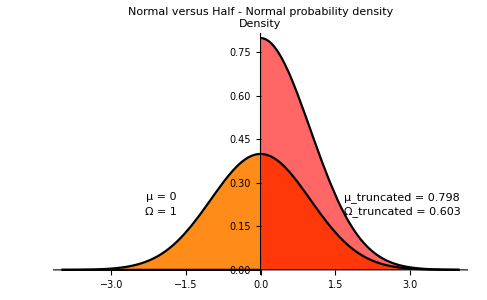

Figure Figure. Standard normal probability density function plot with corresponding half - normal probability density function.

Generally when sampling from truncated distribution on interval B̄<B<B̲  we would do this indirectly by sampling from standard uniform distribution truncated between Φ(B̄) and Φ(B̲) and then use this output value as input in the inverse distribution function Φ^-1 of required distribution Φ to obtain sampled value. In Mathematica Wolfram, however, we will be using function TruncatedDistribution for this purpose.

To sum up, we will be making a draw from right half normal posterior (S/2)_posterior\[Distributed]ϕ^+(μ_B^*,Ω_B^*), where μ_B^* and Ω_B^* are parameters of truncated normal posterior distribution function computed as in unrestricted case of normal priors in equation (EquationNumbered).

##### Simulation of error variance given the coefficients

Lets now assume that B in (EquationNumbered) is known. Usually when specifying variance prior the most appealing distribution is inverted gamma. If the prior for variance is (σ_(ε, prior))^2\[Distributed]IΓ(α,β) where IΓ represents inverted gamma distribution, then the posterior for (σ_(ε, posterior))^2 is:

(σ_(ε, posterior))^2\[Distributed]IΓ(α^*,β^*)

, where

α^*=α+T/2

and

β^*=(β^-1+∑_(i=1)^T ε_i^2).

Results in 36-39 follow from standard Bayesian linear regression treatment and can be found in similar form on Wikipedia page on Bayes regression.

#### Section.Subsection.Subsubsection Deriving latent data posterior densities

At this point S/2 and σ_ε are known and latent variable Q’s is random. The problem of deriving conditional posterior distribution f(Q|σ_ε,S/2,ΔP) is a little bit more complicated and computationally more intensive in comparison to the previous two cases where we used already given solutions from Bayesian regression. The burden comes from the fact that here we have a series of values rather than just one. As mentioned before, although we could in theory obtain exact joint posterior, in reality this is unfeasible due to large number of combinations. Instead we will be using Gibbs sampler technique here also and, as mentioned before, we will obtain f(Q|σ_ε,S/2,ΔP) by iterating Gibbs sequence draws from Q's full conditional posterior distributions f(Q_1|σ_ε,S/2,ΔP,Q_-1),...,f(Q_N|σ_ε,S/2,ΔP,Q_-T). We now turn to derivations of these posteriors.

As a starting point we look at the equation (EquationNumbered):

ΔP_t=S/2 ΔQ_t+ε_t.

Having in mind that we are in Bayes domain we start from a formal definition of posterior for t^th observation:

ℙ(Q_t|σ_ε,S/2,ΔP,Q_-t)=(ℙ(ΔP|σ_ε,S/2,Q_t,Q_-t)·ℙ(Q_t|σ_ε,S/2,Q_-t))/(ℙ(ΔP|σ_ε,S/2,Q_-t)).

Furthermore, we treat ℙ(ΔP|σ_ε,S/2,Q_-t) as a constant since it does not depend on Q_t so that it can be disregarded at this point in order to simplify the derivations. In fact, if there is a need for a complete density in later calculations, once the posterior distribution kernel is obtained, we would just scale this kernel in order to integrate up to 1. This is the usual way that constants are dealt with in Bayesian framework.  Equation (EquationNumbered) is now written as:

ℙ(Q_t|σ_ε,S/2,ΔP,Q_-t)∝ℙ(ΔP|σ_ε,S/2,Q_t,Q_-t)·ℙ(Q_t|σ_ε,S/2,Q_-t).

The (EquationNumbered) represents standard way of representation of Bayes theorem in the shape of Posterior∝likelihood×prior. Now, the prior ℙ(Q_t|σ_ε,S/2,Q_-t) will be discussed. The only variable that could have any information about Q_t is price its-self, so that prior ℙ(Q_t|σ_ε,S/2,Q_-t)=ℙ(Q_t)=1/2. Thus by initial assumptions of the Roll’s model ℙ(Q_t|σ_ε,S/2,Q_-t)=1/2 and it is treated as proportionality constant. Finally rewriting the equation (EquationNumbered) as:

ℙ(Q_t|σ_ε,S/2,ΔP,Q_-t)∝ℙ(ΔP|σ_ε,S/2,Q_t,Q_-t),

shows that posterior probability is actually proportional to conditional likelihood of price differences. In order to derive right hand side of (EquationNumbered) equation (EquationNumbered) must be rewritten as two successive price changes.

ΔP_t=S/2(Q_t-Q_(t-1))+ε_t,
ΔP_(t+1)=S/2(Q_(t+1)-Q_t)+ε_(t+1).

Equations in (EquationNumbered) are interesting in a sense that they show the fact which could have been easily (wrongfully) omitted. Namely, information about Q_t can be extracted from two neighbor price differences rather than just one which we would consider if we were to look at equation (EquationNumbered). Another point that needs to be considered by looking at (EquationNumbered) is that we will actually have three different cases of dealing with ℙ(Q_t|σ_ε,S/2,ΔP,Q_-t), in particular, when considering the case t=1 only the lower equation of (EquationNumbered) will be relevant, case when t=N the upper equation is the one that is possible and, finally, in all other cases we will consider both of the equations in (EquationNumbered)9. In addition, for a given index t a set of Q_-t is non informative except for the two neighbor variables Q_(t+1) and Q_(t-1) (the exception are cases t=1 or t=N, when only one equation in (EquationNumbered) is feasible).

We proceed now to detailed derivations of above mentioned statements by expanding r.h.s of (EquationNumbered) i.e. expanding the likelihood:

ℙ(ΔP|σ_ε,S/2,Q_t,Q_-t)=ℙ(ΔP_2|σ_ε,S/2,Q_t,Q_-t)·...·ℙ(ΔP_T|σ_ε,S/2,Q_t,Q_-t)
=ϕ(S/2(Q_2-Q_1),σ_ε)·...·ϕ(S/2(Q_T-Q_(T-1)),σ_ε).

Equation (EquationNumbered) follows from the fact that conditional on everything else ΔP_t has the same distributed as ε_t but with added mean of S/2(Q_t-Q_(t-1)).

Another way of coming to the same conclusion would be to consider ε_t as a function of ΔP_t in the density function of ε_t so that having in mind (EquationNumbered) we could get ε_t(ΔP_t)=ΔP_t-S/2(Q_t-Q_(t-1)). Then, by plugin this substitution into normal density function (since ε_t is normally distributed by initial assumptions) we get that the conditional density of ΔP_t is ϕ(ε_t(ΔP_t)).

The fact that conditional likelihood of price differences ΔP|σ_ε,S/2,Q is jointly distributed as ϕ(ε_2(ΔP_2))·...·ϕ(ε_T(ΔP_T)) derives from the assumption of independence of ε terms. Now, if we return to the equation (EquationNumbered) and bear in mind that l.h.s. of (EquationNumbered) is defined for specific Q_t, every other term that does not have index t in (EquationNumbered) can be treated as proportionality constant in regards to l.h.s. of (EquationNumbered).

Plugin (EquationNumbered) in (EquationNumbered) and applying last statement leaves us to before mentioned three cases:

t=1, (EquationNumbered) is rewritten as:

ℙ(Q_1|σ_ε,S/2,ΔP,Q_-1)∝ϕ(S/2(Q_2-Q_1),σ_ε),

furthermore, since Q_-1 and ΔP are uninformative except for Q_2 and ΔP_2 then ℙ(Q_1|σ_ε,S/2,ΔP,Q_-1) can be rewritten as ℙ(Q_1|σ_ε,S/2,ΔP_2,Q_2);

t=T, (EquationNumbered) is rewritten as:

ℙ(Q_T|σ_ε,S/2,ΔP,Q_-T)∝ϕ(S/2(Q_T-Q_(T-1)),σ_ε),

furthermore, since Q_-T and ΔP are uninformative except for Q_(T-1) and ΔP_T then ℙ(Q_T|σ_ε,S/2,ΔP,Q_-T) can be rewritten as ℙ(Q_T|σ_ε,S/2,ΔP_T,Q_(T-1));

1<t<T, (EquationNumbered) is rewritten as:

ℙ(Q_t|σ_ε,S/2,ΔP,Q_-1)∝ϕ(S/2(Q_t-Q_(t-1)),σ_ε)·ϕ(S/2(Q_(t+1)-Q_t),σ_ε),

furthermore, since Q_-t and ΔP are uninformative except for Q_(t-1), Q_(t+1), ΔP_(t-1) and ΔP_t  then ℙ(Q_T|σ_ε,S/2,ΔP,Q_-T) can be rewritten as ℙ(Q_t|σ_ε,S/2,ΔP_t,ΔP_(t+1),Q_(t-1),Q_(t+1)).

#### Section.Subsection.Subsubsection Example

In order to show the performance of Gibbs estimate of Roll’s measure 20 trades were simulated with σ_ε=0.01,S/2=0.01, see Figure Figure. After that, Gibbs procedure was run with number of sweeps set to 10,000 of which first 20%  were taken out as burn in sample so that remaining 8,000 draws are used to describe the posteriors.

```mathematica
ClearAll["Global`*"]
Remove["Global`*"]
SeedRandom@777
𝕍̄=0;
Subscript[σ, ε]=0.01;
S=0.02;
ε[t_]:=ε[t]=RandomVariate[NormalDistribution[0,Subscript[σ, ε]]];
V[1]:=ε[1];
V[t_]:=V[t]=𝕍̄+V[t-1]+ε[t];
Q[t_]:=Q[t]=RandomChoice[{1,-1}];
P[t_]:=P[t]=V[t]+1/2 S Q[t];
T=20;
FundamentalPrice=V/@Range@T;
Price=P/@Range@T;
Qindicators=Q/@Range@T*S/2;
```

```mathematica
Listplot=ListPlot[{Price,FundamentalPrice},PlotStyle->{Directive[Opacity[.6],Red],Directive[Opacity[.99],Orange]},Joined->{True,True},PlotRange->{{0.7,T+.5},Automatic},AspectRatio->0.6,
PlotLabels->{Style["Transaction Price",10],Style["Fundamental Price",10]},
GridLines->Automatic,
AxesStyle->Directive[FontFamily->"Times New Roman",Black,10],GridLinesStyle->Directive[ Dashed]];
arrows=Flatten@Map[Arrow,{{Range@20,FundamentalPrice}ᵀ,{Range@20,Price}ᵀ}ᵀ,{1}];
arrowsPlot=Graphics[{Arrowheads[0.02],Black,arrows},PlotRange->{{0.7,T+.5},Automatic},AspectRatio->0.6];
Show[Listplot,arrowsPlot]
```

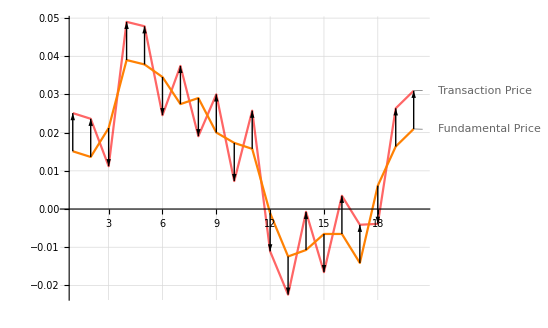

Figure Figure. Simulated time series of 20 transaction prices along with fundamental price process. The arrows are presenting trade indicators. The length of arrows  is representing half bid/ask spread S/2=0.01.

Note: The accuracy of the estimates depends, among other things, crucially on the intensity of the bid/ask spread. The innovation of transaction prices is driven by two effects, namely, the fundamental price innovations effect from ε_t and the effect due to the bid/ask transactions. If the bid/ask spread value is substantial the procedure will succeed to pick it up, so that the bigger the length of arrows on the graph above the more will Gibbs procedure be able to pick up this movement. When  discussing the length of arrows it is being measured in relative to volatility of innovations σ_(ε.)

Priors for half-spread were drawn from right half-normal distribution with parameters μ_B=0 and Ω_Β=1. This implies actual mean √(2/π)=0.798 and variance (1-2/π)=0.363 which is fairly wide for our purpose. Nevertheless, in example given, where actual half-spread and volatility of innovation are much smaller than former mentioned values this only means that we let estimate be more data driven rather than having priors have influence on posteriors. The resulting kernel densities of half-spread S/2 and volatility of innovations σ_ε are shown in the Figure Figure and Figure Figure respectively. The mean value for estimated effective cost of trade is 0.00998 which is fairly close to actual value of S/2=0.01 and the value of volatility of innovation term is 0.00996 which is, again, close to the actual value of σ_ε=0.01. In addition, kernel densities are resembling a lot to normal and inverse gamma distributions. On the other hand, moment based estimate of half-spread is 0.01340 which implies innovations with standard error of 0.0064510.

```mathematica
(*Gibbs sampling from 3 conditional distributions*)
(*P     - prices vector
qinit - initial values for q, a vector of size Length[P]
σinit - initial value for σ
μc    - prior parameter for truncated normal distribution mean
Ωc    - prior parameter for truncated normal distribution standard deviation
AlphaPrior - alpha parameter for gamma distribution prior for σ
BetaPrior - beta parameter for gamma distribution prior for σ*)

Gibbss[P_List,qinit_List,σinit_,μc_,Ωc_,AlphaPrior_,BetaPrior_,sweep1_,OptionsPattern[]]:=Module[{σ=σinit,
q=qinit,qdummy,c=0,ΔP=Δ[P],n=Length[P]},

Table[
(*update q vector after first and every next sweep fro values from array q[i]*)
(*Begin with starting values of q*)
Table[qdummy[i]:=q[[i]],{i,n}];
c=GenerateC[ΔP,Δ[q],σ,μc,Ωc];
σ=Generateσ[ΔP,c,Δ[q],AlphaPrior,BetaPrior,n-1];
q=Generateq[ΔP,c,σ,n,qdummy];
{σ,c,q},
{sweep1}]
]

(*___________________generating c______________*)
Options[GenerateC]={DistributionParameter1->{0,∞}};
GenerateC[ΔP_,Δq_,σ_,μc_,Ωc_,OptionsPattern[]]:=RandomVariate[
dist[
OptionValue[DistributionParameter1],
μpost[ΔP,Δq,σ,μc,Ωc],
Sqrt@PosteriorCov[Δq,σ,Ωc]
]
];

(*Creating function for truncated normal distribution*)
dist[truncRegion_,distPar1_,distPar2_]:=TruncatedDistribution[truncRegion,NormalDistribution[distPar1,distPar2]]

(*Functions for Creating posteriors for μc and Ωc*)
μpost[ΔP_,Δq_,σ_,μc_,Ωc_]:=d[ΔP,Δq,σ,μc,Ωc]*𝔻[Δq,σ,Ωc]

(*P0sterior mean of c as a function of d and SigmaPost (posterior standard error of estimate)*)
𝔻i[Δq_,σ_,Ωc_]:=Total[Δq*Δq]/σ^2+1/Ωc^2;
𝔻[Δq_,σ_,Ωc_]:=1/𝔻i[Δq,σ,Ωc];
PosteriorCov[Δq_,σ_,Ωc_]:=𝔻[Δq,σ,Ωc];


(*posterior standard error of estimate*)
d[ΔP_,Δq_,σ_,μc_,Ωc_]:=1/σ^2 Total[ΔP*Δq]+μc/Ωc^2;(*Look any text on bayes regression, only difference is that we are using here univariate regression*)


(*________________generating σ__________________*)
Generateσ[ΔP_,c_,Δq_,AlphaPrior_,BetaPrior_,N_]:=1/Sqrt[Generateσsqrℐnverse[ΔP,c,Δq,AlphaPrior,BetaPrior,N]];

(*residuals from bayes regression*)
e[ΔP_,c_,Δq_]:=ΔP-c  Δq

(*alpha posterior*)
AlphaPost[AlphaPrior_,N_]:=AlphaPrior+N/2

(*beta posterior*)
BetaPost[BetaPrior_,ΔP_,c_,Δq_]:=BetaPrior+Total[(e[ΔP,c,Δq]^2)]/2

(*generate σsqr posterior from gamma dist*)
Generateσsqrℐnverse[ΔP_,c_,Δq_,AlphaPrior_,BetaPrior_,N_]:=RandomVariate[
GammaDistribution[AlphaPost[AlphaPrior,N],1/BetaPost[BetaPrior,ΔP,c,Δq]
]
]


(*Generating latent time series_______*)
(*of q's, depending on case, 1st,_____*)
(*middle or last_____________________*)

Generateq[ΔP_,c_,σ_,n_,qdummy_]:=Table[
If[i==1,qdummy[i]=Generate𝒬First[qdummy[i+1],ΔP[[i]],c,σ],
If[i==n,qdummy[i]=Generate𝒬Last[qdummy[i-1],ΔP[[i-1]],c,σ],
qdummy[i]=Generate𝒬T[qdummy[i-1],qdummy[i+1],ΔP[[i-1]],ΔP[[i]],c,σ]]],{i,n}
];

Generate𝒬T[qbefore_,qafter_,ΔP1_,ΔP2_,c_,σ_]:=RandomChoice[{q𝒟istT[qbefore,qafter,ΔP1,ΔP2,c,σ][1],q𝒟istT[qbefore,qafter,ΔP1,ΔP2,c,σ][-1]}->{1,-1}];

q𝒟istT[qbefore_,qafter_,ΔP1_,ΔP2_,c_Real,σ_][q_]:=Evaluate[ⅇ^((c^2 (4-2 q^2+qafter^2+qbefore^2+2 q (qafter+qbefore))+2 c (q+qbefore) ΔP1+ΔP1^2-2 c (q+qafter) ΔP2+ΔP2^2)/(2 σ^2))/(ⅇ^(((c+c qbefore+ΔP1)^2+(c+c qafter-ΔP2)^2)/(2 σ^2))+ⅇ^(((c (-1+qbefore)+ΔP1)^2+(c-c qafter+ΔP2)^2)/(2 σ^2)))];

Generate𝒬First[q2_,ΔP1_,c_,σ_]:=RandomChoice[{q𝒟istFirst[q2,ΔP1,c,σ][1],q𝒟istFirst[q2,ΔP1,c,σ][-1]}->{1,-1}];

q𝒟istFirst[q2_,ΔP1_,c_,σ_][q_]:=Evaluate[(ⅇ^((c^2 (2-q^2+2 q q2+q2^2)-2 c (q+q2) ΔP1+ΔP1^2)/(2 σ^2)))/(ⅇ^((c+c q2-ΔP1)^2/(2 σ^2))+ⅇ^((c-c q2+ΔP1)^2/(2 σ^2)))];

Generate𝒬Last[qbefore_,ΔP_,c_,σ_]:=RandomChoice[{q𝒟istLast[qbefore,ΔP,c,σ][1],q𝒟istLast[qbefore,ΔP,c,σ][-1]}->{1,-1}];

q𝒟istLast[qbefore_,ΔPbefore_,c_,σ_][q_]:=Evaluate[(ⅇ^((c^2 (2-q^2+2 q qbefore+qbefore^2)+2 c (q+qbefore) ΔPbefore+ΔPbefore^2)/(2 σ^2)))/(ⅇ^((c (-1+qbefore)+ΔPbefore)^2/(2 σ^2))+ⅇ^((c+c qbefore+ΔPbefore)^2/(2 σ^2)))];

(*____Differencing time series function______*)
Δ[x_List]:=x[[2;;All]]-x[[1;;-2]];
```

```mathematica
ΔPrice=Δ[Price];
initialq=Sign/@ΔPrice;
initialq=Prepend[initialq,1];
sweep=10000;
burn=sweep/5;
σinit=0.01;
μc=0;
Ωc=1;
αprior=10^-6;
βprior=10^-6;
```

```mathematica
draws=Gibbss[Price,initialq,σinit,μc,Ωc,αprior,βprior,sweep];
GibbsRollMean=Mean[draws[[All,2]][[burn+1;;All]]];
GibbsRollMedian=Median[draws[[All,2]][[burn+1;;All]]];
GibbsRollVolatility=Mean[draws[[All,1]][[burn+1;;All]]];
MomentRollMean=Sqrt[-Covariance[ΔPrice[[2;;All]],ΔPrice[[1;;-2]]]];
MomentRollVolatility=Sqrt[Variance[ΔPrice]-2 MomentRollMean^2];
```

```mathematica
GraphC=SmoothHistogram[
draws[[All,2]][[burn+1;;All]],
PlotRange->All,
Filling->Axis,FillingStyle->Directive[Opacity[.6],Red],
AxesLabel->{"S/2","Density"},AxesStyle->Directive[FontFamily->"Times New Roman",Black,10],
PlotStyle->Directive[Thick,Black],
GridLines->{{{S/2,Directive[Thick,Black,Opacity[1]]}}}
]
```

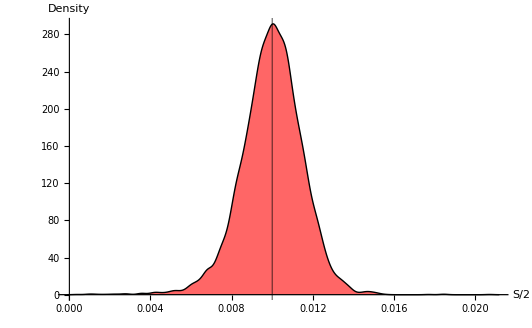

Figure Figure. Kernel density of posterior half-spread estimate of simulated transaction prices process with S/2=0.01 and σ_ε=0.01. Posterior is drawn from truncated normal distribution of priors  with parameters μ_(prior,trunc) = 0 and σ_(prior,trunc) = 1.

```mathematica
Graphσ=SmoothHistogram[
draws[[All,1]][[burn+1;;All]],
PlotRange->{{0,0.022},{0,210}},
Filling->Axis,FillingStyle->Directive[Opacity[.6],Red],
AxesLabel->{"σ_ε","Density"},AxesStyle->Directive[FontFamily->"Times New Roman",Black,10],
PlotStyle->Directive[Thick,Black],
GridLines->{{{Subscript[σ, ε],Directive[Thick,Black,Opacity[1]]}}}
]
```

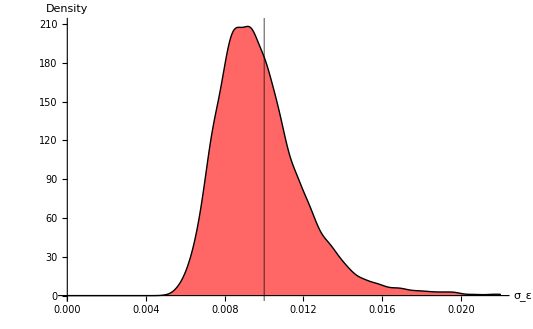

Figure Figure. Kernel density for the posterior estimate of volatility. σ_ε of innovation term ε_t from simulated transaction prices process with S/2=0.01 and σ_ε=0.01. Priors are drawn from inverse gamma distribution with parameters α=10^-6 and β=10^-6.

Although, one can be tempted to conclude that Gibbs estimators are more efficient than moment based, this is generally a false statement. Firstly, the case discussed is based on rather small sample of 20 prices and is vastly influenced by the randomness of the sample. Secondly, when dealing with small samples the Gibbs estimate is usually largely influenced by priors thus it tends to be biased. Even though this is not the case here in practical simulation more realistic priors would be chosen hence the posterior estimate would be influenced more by prior than here. Thirdly, the moment based effective cost estimate will, on average, be higher than Gibbs one, exactly like seen here. The reason is that moment based estimate picks up all of the sample price changes of autocovariance to the effective cost of trade, see Hasbrouck (2004).

In general, it can not be stated with certainty which parameter is closer to the true value, but Gibbs estimate does give us two clear advantages over moment based. First one is before mentioned positivity boundary on the estimate. Second one is that we can get the estimated series of probabilities of trade direction indicators Q's, see Figure Figure.

```mathematica
Qgibbs = draws[[burn + 1 ;; All, 3]];
QgibbsMean = Table[Mean[Qgibbs[[All, i]]], {i, T}];
gibbsround = If[#>0,1,-1]&/@QgibbsMean;
NuOfHits = Table[If[gibbsround[[i]] == Q[i], 1, 0], {i, T}] // Total;Graphq=ListPlot[
{Q/@Range@T,QgibbsMean},
PlotRange->{-1.03,1.03},
Frame->True,FrameStyle->Directive[Black,FontFamily->"Times New Roman",Black],FrameLabel->{Style["Time",FontFamily->"TimesNewRoman",13],Style["E[q(t)]",FontFamily->"TimesNewRoman",13]},
Filling->{1->None,2->Axis},FillingStyle->Directive[Thickness[0.0035],Red,Opacity[0.6]],
AxesStyle->Directive[FontFamily->"Times New Roman",Black],
PlotLabel->Style["Actual and simulated trade directions from Gibbs sampler\n number of hits = "<>ToString@NuOfHits,Black,FontFamily->"Times New Roman",11],
LabelStyle->{Alignment->Right},
PlotStyle->{Directive[Black],Directive[Opacity[0]]},
Epilog->{Text[Style["+1 (Buy)",Black,FontFamily->"Times New Roman",13],{-1,1.25}],
Text[Style["-1 (Sell)",Black,FontFamily->"Times New Roman",13],{-1,-1.25}]},
ImagePadding->40,PlotRangeClipping->False
];
```

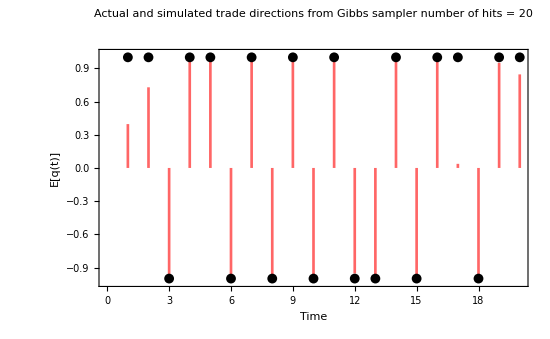

Figure Figure. Estimated trade directions. Dots are representing actual transaction indicators while red lines are representing calculated expected-average  indicators from sample of 8,000 draws of all 20 bid-ask indicators from Gibbs sampler.

Figure Figure shows that in this example we have been able to predict all 20 trade directions which by itself presents a great result. In practice, however this is hardly achievable, in fact experimenting with same sampling procedure as here (same S/2 and σ_ε) we achieved average hit to total ratio of around 85%-90%. In this exercise most of the indicators are close to actual values with exception of number 17 which could have easily happen to be a miss. In a practical sense these hit/miss ratios can be used to get the overall feel of how “accurate” the model is since the better the hit/miss ratio in Q's the better we can expect the whole joint density of posterior of S/2 and σ_ε to be. Naturally, the greater the actual effective cost the more accurate are posterior densities since the overall process can do a better job in discriminating the volatility of effective cost from the volatility of the innovation term. Henceforth, in markets with relatively small effective cost we can expect poor performance of both kinds of estimates.

Finally, a contour plot and smooth 3D histogram of posterior joint density of S/2 and σ_ε are presented in Figure Figure.

```mathematica
data=draws[[All,{1,2}]][[burn;;All]];
dhist=SmoothDensityHistogram[data,Mesh->10,PlotRange->{{0.005,0.017},{0.005,0.015}},LabelStyle->Directive[FontFamily->"Calibri"],FrameLabel->{Style["σ_ε",Bold,FontFamily->"TimesNewRoman",14],Style["S/2",FontFamily->"TimesNewRoman"]},ColorFunction->ColorData["SolarColors"]];dhist3d=SmoothHistogram3D[data,PlotRange->{{0.005,0.017},{0.005,0.015}},Mesh->10,LabelStyle->Directive[FontFamily->"Calibri"],AxesLabel->{Style["σ_ε",Bold,FontFamily->"TimesNewRoman",14],Style["S/2",FontFamily->"TimesNewRoman"]},ColorFunction->"SolarColors"];
GraphicsGrid[{{dhist,dhist3d}}]
```

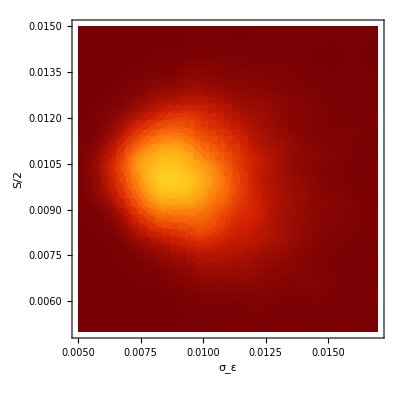

Figure Figure. Posterior  contour and posterior density plots of joint density posterior of half-spread and volatility of innovation term.

### SectionNumber.Subsection Empirical evidence and extensions

Huang & Stoll (1994) found that in the case of NYSE Roll's measure is much lower than the effective spread and in case of NASDAQ it is almost same as effective spread. However, Hasbrouck (2006) finds that Roll's measure is too low when compared to effective spread on NYSE but when adjusted to observed trade prices which are on average 0.0079($/share) away from midpoint it gives a relatively close estimate.

Many generalization of Roll’s implied spread have been presented through the years, the most cited include model of Glosten & Harris (1988) who expand the model so that spread is presented as sum of adverse and transitory selection components; model Huang & Stoll (1997) who introduce three part decomposition of spread; model of Holden (2009) who extends the Roll’s model in order to accommodate data for days with no trading. Papers that bring some broader introduction on the concept of liquidity measures include, among the others, Gabrielsen et al. (2011). An overall overview of the market microstructure topic can be found in Hasbrouck (2007), de Jong & Rindi (2009) and O'hara (1995).

## The methodology of GARCH estimation

In modern risk management VaR and ES estimation is performed by means of historical simulation, Monte Carlo methods or by modeling volatility  of assumed distribution. Volatility modeling can be further divided as Generalized Auto Regressive Conditional Heteroskedasticity (from now on: GARCH) modeling and stochastic volatility modeling. Volatility modeling using GARCH model, introduced by Engle (1982) and Bollerslev (1986), has gained much popularity in recent years. This approach makes distributional assumptions about asset returns which is in line with VaR and ES formulas derived so far. GARCH modeling, depending whether we are concerned with single asset or portfolio of assets, can further be classified as univariate and multivariate modeling, later of which takes into account asset correlation and diversification effect. Obstacles concerning higher dimensionality GARCH models are well documented in literature, for example see Alexander (2009). In this section univariate GARCH models will be described, in particular, simple GARCH, EWMA as a special case of GARCH and EGARCH. Although not described here, multivariate DCC GARCH and Orthogonal GARCH of Alexander & Chibumba (1997) models are presented as a part of before mentioned  Mathematica package manual at the end of this paper. The theory behind estimation, forecasting, and distributional assumptions of univariate models will be presented as main topic. Three distribution will be assumed, namely, Normal, Student  and Generalized Error Distribution. At the beginning of this section stylized facts of financial returns will be concisely described, followed by already mentioned theoretical description of univariate GARCH models. The final part of section is devoted to choices of "most suitable" GARCH model, estimation sample size and software available for GARH volatility estimation. As a result of working on this master thesis special functions were programmed for GARCH estimation in Wolfram language, short introduction with pointers for further exploration will be briefly described. Most of the derivation and discussion presented here will be following closely 4th chapter of the book Financial Modeling Under Non-Gaussian Distributions, 2007 by Eric Jondeau, Ser-Huang Poon, Michael Rockinger.

Other references will be given in text.

### Section.Subsection Financial returns

From a general point of view, there are various factors across various market that are differently impacting specific asset price properties so one would not expect values of two "diametrically" different assets to exhibit similar statistical properties, but nevertheless more than fifty years of empirical research of financial time series has found that indeed there are some broad statistical properties that are common for all assets called stylized empirical facts in literature. Here we count some common set of stylized facts about financial returns closely following  Cont (2001):

Assets returns exhibit insignificant autocorrelation.

Unconditional distributions of returns are exhibiting heavy tails.

Returns are exhibiting gain/loss asymmetry.

Returns are more likely to be normally distributed if we increase time period over which we are calculating them.

Returns are displaying, invariability to scale, a high degree of variability - intermittency.

High volatility happens in clusters.

Even after correcting returns for volatility clustering, the residual time series still exhibit heavy tails although smaller than earlier.

The autocorrelation function of absolute returns decays slowly as a function of the time lag by power low.

Most measures of volatility of an asset are negatively correlated with the returns of that asset - leverage effect.

Trading volume is correlated with all measures of volatility - volume/volatility correlation.

GARCH models have been successfully capturing several features of these return properties, for example clustering, autocorrelation, heavy tails, and leverage which is modeled with asymmetric GARCH models. The structure of volatility models can be described as:

R_t=μ_t(θ)+ε_t
ε_t=σ_t(θ)·z_t,

where

µ_t(θ)=E[R_t|ℐ_(t-1)], and
σ_t^2(θ)=E[(R_t-μ_t(θ))^2|ℐ_(t-1)].

In (EquationNumbered), the return R_t is decomposed into a conditional mean μ_t(θ) and a residual term ε_t. The dynamics of the conditional mean μ_t(θ) may be an ARMA (p, q) process or it could consist of seasonality features although several papers show that modeling conditional mean does not improve accuracy of prediction (Angelidis, Benos, & Degiannakis, 2004). ℱ_t is the information set available at time t. It may include current and past returns, current and past residuals, or any other variable known at time. According to (EquationNumbered), the residual term ε_t has a volatility conditional on the information available at time t-1, denoted ℐ_(t-1), which may vary over time. θ is the vector of unknown parameters. The variable z_t will be assumed to follow some distribution with mean 0 and variance 1. Even though normality will be assumed as one of conditional distributions later in this section, this need not be the case in reality. Other distributions such as the Student  and Generalized Error distribution will be discussed as a way to overcome this deficiency.

Next subsection will be describing GARCH modeling of conditional variance σ_t^2(θ).

### Section.Subsection GARCH model

The Auto Regressive Conditional Homoskedasticity (ARCH) model σ_t^2=ω +∑_(i=1)^p α_i ε_(t-i)^2, originally introduced by Engle (1982), has shown that, due to the large persistence in volatility, it needs a large numbers of observations in order fit the data well. Bollerslev (1986) further extends ARCH by adding variance term in equation, giving more parsimonious solutions. The conditional variance of a GARCH  is:

σ_t^2=ω +∑_(i=1)^p α_i ε_(t-i)^2+∑_(j=1)^q β_j σ_(t-j)^2.

For this model to be well defined and the conditional variance to be positive, the parameters must satisfy the following constraints: ω>0,α_i≥0,i=1,...,p,β_j≥0, for j=1,...,q.

It follows that the unconditional variance is given by:

σ^2=ω/(1-∑_(i=1)^p α_i-∑_(j=1)^q β_j).

Therefore, the process ε_t is covariance stationary if and only if ∑_(i=1)^p α_i+∑_(j=1)^q β_j<1. Notice that this is a sufficient but not necessary condition for it to be strictly stationary (Bollerslev, 1986; Bougerol & Picard, 1992; Nelson, 1990). To see why, assume the following GARCH(1, 1) model:

σ_t^2=ω+α_1 ε_(t-1)^2+β_1 σ_(t-1)^2.

This model can be rewritten by successive iterations:

σ_t^2=ω+σ_(t-1)^2 (α_1 z_(t-1)^2+β_1)=ω(1+∑_(t=1)^∞ ∏_(k=1)^t (α_1 z_(t-k)^2+β_1)).

Then, for this expression to converge toward a finite limit, so that the process ε_t is strictly stationary, we need next condition to be satisfied

E[log(α_1 z_(t-1)^2+β_1)]<0

We see that, due to the Jensen’s inequality,

E[log(β_1+α_1 z_(t-1)^2)]≤ log(E[β_1+α_1 z_(t-1)^2])= log (α_1+β_1)

, so that, even when α_1+β_1=1, the process is still strictly stationary.

#### Section.Subsection.Subsubsection Forecasting

Forecasts of the GARCH model are obtained recursively. The 1-step ahead forecast for σ_(t+1)^2 is:

σ_t^2(1)=ω̂+α̂(ε̂)_(t-1)+β̂(σ̂)_(t-1).

Since ε_t^2=σ_t^2 z_t^2, the GARCH(1, 1) model can be rewritten as:

σ_t^2=ω +α_1 ε_(t-1)^2+β_1 σ_(t-1)^2=ω +(α_1+β_1)σ_(t-1)^2+α_1 σ_(t-1)^2(z_(t-1)^2-1),

so that, at time t+2 , we have

σ_(t+2)^2=ω+(α_1+β_1)σ_(t+1)^2+α_1 σ_(t+1)^2(z_(t+1)^2-1)

with E[(z_(t+1)^2-1)|ℐ_t]=0. We deduce the following 2-step ahead forecast for σ_(t+2)^2:

σ_t^2(2)=ω̂+(α̂+β̂)σ_t^2(1).

Generally speaking, the k_th-step ahead forecast for σ_(t+κ)^2  is

σ_t^2(κ)=ω̂+(α̂+β̂)σ_t^2(κ-1)

for κ>1. Alternatively, this last equation can be expressed as

σ_t^2(κ)=σ̂+(α̂+β̂)^(κ-1)(σ_t^2(1)-σ̂)

for  κ>1, where σ̂=ω̂/(1-α̂-β̂).  Therefore we can see that  σ_t^2(κ)→σ̂ as κ→∞. In reality α  and β sum is very close to 1. This property motivated exploration of limit case model called an integrated GARCH, in which α+β=1.

#### Section.Subsubsection.Subsubsection Estimation

We will consider here the Maximum Likelihood, ML estimation of a GARCH  model with innovations from normal distribution but we emphasize that for any other distributional assumption and/or GARCH-type model the methodology is conceptually identical. Assuming that we have a time series of returns {R_1, ⋯, R_T}, and denote m= max (p, q) the number of observations lost for initializing the process. Under the normality assumption, the likelihood function of a GARCH  model is

f(ε_1,..., ε_T|θ)=f(ε_T|ℱ_(T-1))·f(ε_(T-1)|ℱ_(T-2))·...·f(ε_(m+1)|ℱ_m)·f(ε_1,..., ε_m|θ)
=∏_(t=m+1)^T 1/(√(2π σ_t^2)) exp(-ε_t^2/(2 σ_t^2))·f(ε_1,..., ε_m|θ)

where θ=(ω, α_1,..., α_p, β_1,..., β_q)'  is the vector of unknown parameters and f(ε_1 ,…, ε_m|θ) is the joint PDF of (ε_1 ,…, ε_m).  In general, this term is simply dropped, to avoid specifying the joint distribution of the first observations. It is possible to justify this by observing that this term represents only one term in usually long sequence of numbers. Omitting this term only introduces a negligible error in the likelihood. Hence, we focus on the conditional likelihood function:

f(ε_(m+1),..., ε_T|θ, ε_1,..., ε_m)=∏_(t=m+1)^T 1/(√(2π σ_t^2)) exp (-ε_t^2/(2 σ_t^2)).

The ML estimator is obtained by maximizing this expression or, equivalently, the log-likelihood function:

L_T(θ|R_t, t =1,..., T)=∑_(t=m+1)^T ℓ_t(θ),

where

ℓ_t(θ)=-1/2 log(2π)-1/2 log(σ_t^2)-ε_t^2/(2 σ_t^2),

is the log-likelihood of the observation t , with ε_t=R_t-μ_t(θ).

Applying the derivative on log-likelihood function yields the gradient:

(∂ℓ_t(θ))/(∂θ)=-1/(2 σ_t^2)(∂σ_t^2)/(∂θ)+ε_t^2/(2 σ_t^4)(∂σ_t^2)/(∂θ)=1/(2 σ_t^2)(∂σ_t^2)/(∂θ)(ε_t^2/σ_t^2-1)

where we know that:

(∂σ_t^2)/(∂ω)=1,
(∂σ_t^2)/(∂α_i)=ε_(t-i)^2,for i=1,…, p,
(∂σ_t^2)/(∂β_j)=σ_(t-j)^2,for j=1,…, q.

The second-order derivatives yield a matrix called Hessian, consisting of terms such as

(∂^2 ℓ_t(θ))/(∂θ∂θ’)=-1/(2 σ_t^2)(∂σ_t^2)/(∂θ)(∂σ_t^2)/(∂θ’)ε_t^2/σ_t^2+(ε_t^2/σ_t^2-1)∂/(∂θ')(1/(2 σ_t^2)(∂σ_t^2)/(∂θ)),

where,

E[(∂^2 ℓ_t(θ))/(∂θ∂θ’)]=-E[1/(2 σ_t^2)(∂σ_t^2)/(∂θ)(∂σ_t^2)/(∂θ’)ε_t^2/σ_t^2+(ε_t^2/σ_t^2-1)∂/(∂θ')(1/(2 σ_t^2)(∂σ_t^2)/(∂θ))]
=-E[1/(2 σ_t^2)(∂σ_t^2)/(∂θ)(∂σ_t^2)/(∂θ’)]

If we define ξ_t=(1, ε_(t-1)^2,…, ε_(t-p)^2, σ_(t-1)^2, …, σ_(t-q)^2)', we may writeσ_t^2=ξ'_t θ, so that,

E[(∂^2 ℓ_t(θ))/(∂θ∂θ’)]=-E[(ξ_t ξ'_t)/(2 σ_t^2)]

The covariance matrix of the ML estimator is given by the inverse of the information matrix, which is defined as minus the expected Hessian:

I(θ)=-E[(∂^2 ℓ_t(θ))/(∂θ∂θ’)]=E[(ξ_t ξ'_t)/(2 σ_t^2)].

This expression can be estimated like this:

Î(θ)=1/(2T)∑_(t=1)^T (ξ̂ OverHat[ξ'])/(σ̂).

Provided standardized innovations have finite fourth moments, the ML estimator is consistent and has the following asymptotic distribution:

√T(θ̂-θ)⇒𝒩(0, (I(θ))^-1) .

For a regression model of the type:

R_t=X_t δ+ε_t,
ε_t=σ_t z_t,
σ_t^2=ω+∑_(i=1)^p α_i ε_(t-i)^2+∑_(j=1)^q β_j σ_(t-j)^2,

where X_t is a set of exogenous explanatory variables and δ  a set of unknown parameters pertaining to the conditional mean equation, we should estimate parameters δ and θ simultaneously. Fortunately, it turns out that the second derivatives of the regression model log-likelihood are such that (Engle, 1982):

E[(∂^2 ℓ_t(θ,δ))/(∂θ∂δ')]=0

Consequently, the information matrix is block-diagonal and the two sets of parameters can be estimated separately.

In practice, the estimation of a GARCH and GARCH type models should be performed, formally, as follows:

Estimate the mean equation R_t=μ_t+ε_t. Calculate ε_t=R_t-μ̂ and σ̂=1/T∑_1^T (ε̂)_t

Select initial values for θ, say θ^0=(ω^0, α_1^0, …, α_p^0, β_1^0, …, β_q^0…) and set (ε̂)_1^2=…=(ε̂)_m^2=(σ̂)_1^2=…=(σ̂)_m^2=(σ̂)^2, with m= max (p, q).

Compute the conditional variance (σ̂)_t^2 for t=m+1,…,T.

Compute the log-likelihood:

L_T(θ^0)=∑_(t=m+1)^T ℓ_t(θ^0)

Change the value of parameters to say  θ^1, so that the log-likelihood increases

L_T(θ^1)>L_T(θ^0).

Iterate steps 3 and 4 until convergence of the log-likelihood to a fixed value is reached.

#### Section.Subsection.Subsubsection Kurtosis of GARCH process

GARCH processes have excess kurtosis. Even if the conditional distribution for the standardized innovations z_t=(R_t-μ_t(θ))/σ_t(θ) is assumed to be normal, the unconditional distribution for ε_t has fatter tails than the normal distribution. For example, consider a GARCH(1, 1) model:

σ_t^2(θ)=ω+α_1 ε_(t-1)^2+β_1 σ_(t-1)^2,

where ε_t=σ_t z_t. The unconditional variance is given by σ^2=ω/(1-α_1-β_1) so that we should have α_1+β_1<1 for σ^2 to be finite. Now, under normality, the conditional fourth moment is given by

E[ε_t^4|ℱ_(t-1)]=E[σ_t^4 z_t^4|ℱ_(t-1)]=3E[σ_t^4|ℱ_(t-1)]=3(ω+α_1 ε_(t-1)^2+β_1 σ_(t-1)^2)^2

, so that when we divide it with  ([E[ε_t^2|ℱ_(t-1))])^2=(ω+α_1 ε_(t-1)^2+β_1 σ_(t-1)^2)^2 we can see that conditional kurtosis is 3 whereas the unconditional fourth moment is:

m_4=E[ε_t^4]
=E[E[σ_t^4 z_t^4|ℱ_(t-1)]]
=3E[σ_t^4]=3E[E[σ_t^4|ℱ_(t-1)]]
=3E[(ω+α_1 ε_(t-1)^2+β_1 σ_(t-1)^2)^2]
=3(ω^2+2 ω α_1 σ^2+α_1^2 m_4+2 ω β_1 σ^2+2 α_1 β_1 m_4/3+β_1^2 m_4/3)
⇒m_4=3(ω^2(1+ α_1+β_1))/((-1+α_1+β_1) (-1+3 α_1^2+2 α_1 β_1+β_1^2))

, where we used the fact that unconditional variance, σ^2, equals ω/(1 -α_1-β_1). Now we can calculate the unconditional kurtosis of GARCH process κ as:

κ=m_4/((E[σ_t^2])^2)
=m_4/σ^4
=3+(6 α_1^2)/(1-2 α_1^2-(α_1+β_1)^2)

which exceeds 3 for  α_1>0, β_1>0, α_1+β_1<1 ,  0<α<1/(√3) and 0<β<-α+√(1-2 α^2).

So, the excess kurtosis is always positive (for before mentioned conditions) and the tails of the distribution of ε_t  are fatter than that of a normal distribution, even if the conditional distribution is normal.

Besides of capturing volatility clusters, GARCH models also capture fat-tailedness of the distribution, however not all the tailedness is captured even with GARCH process, and for that reason we will consider distributions with fatter tails than normal in upcoming sections.

### Section.Subsection Asymmetric GARCH processes

Although GARCH models are able to capture volatility clustering and distribution fat-tails, in these models, positive and negative past values have a symmetric effect on the conditional variance. As mentioned in stylized fact 9, leverage effect is observed as a trend in which negative returns tend to be followed by larger increases in volatility than equally large positive returns.

Pagan & Schwert (1990) and Engle & Ng (1993) proposed the concept of news impact curve. News impact curve describes how new information is incorporated into volatility estimates and it can be formally presented as σ_t^2=f(z_(t-1)). For asymmetric models, the curve is designed to increase differently in the two directions. Figure Figure shows comparison of two news impact curves, we can see that GARCH curve is a quadratic function centered on z_(t-1)=0, however for exponential GARCH (from now on called EGARCH) the curve is asymmetric monotonically decreasing without a minimum,  intersecting GARCH curve at her minimum (curves are plotted on fitted coefficients from S&P returns for 2004-2014). For GARCH model the effect of shock is the same regardless of sign of shock, on the other hand, EGARCH model we notice a much stronger effect of shock to volatility when its sign is negative. This behavior will be clearer once we introduce EGARCH model equation in next subsection.

Several models have been proposed in order to capture asymmetric response of volatility to random shocks (i.e. leverage) in literature. To mention some of them, we have the Exponential GARCH (EGARCH) model of Nelson (1991) which will be used in this thesis, the Threshold GARCH (TGARCH) of Zakoian (1994), the GJR model of Glosten, Jagannathan, & Runkle (1993), the Absolute GARCH (AGARCH) model of Hentschel (1995), APARCH model of Ding, Grange, and Engle (1993).

-Graphics-

Figure Figure. Comparison of typical news impact curves for GARCH and EGARCH models.

#### Section.Subsection.Subsubsection EGARCH model

The Exponential GARCH (EGARCH) introduced by Nelson (1991) has a purpose to improve two imperfections of vanilla GARCH model:

Parameters α and β  have to be constrained during the course of the estimation in order to guarantee conditional volatility positivity;

Empirical evidence suggests an asymmetric response of volatility to shocks;

In the EGARCH model, σ_t^2  depends on both the size and the sign of lagged shocks:

log(σ_t^2)=ω+∑_(i=1)^p g(z_(t-i))+∑_(j=1)^q β_j log(σ_(t-j)^2)

where g(z_t)=[γ(|z_t|-E[|z_t|])+ψ z_t]. Like this, parameters are not imposed to be positive, since the conditional volatility is always positive. The process is strictly and covariance stationary if and only if∑_(j=1)^q β_j<1.  Notice that E[|z_t|]=√(2/π)  under normality.

This specification introduces the desired asymmetry in the following way. Over the range 0<z_t<∞,g(z_t) is linear in z_t with slope γ+ψ, whereas over the range-∞<z_t≤0,g(z_t) is linear in z_t with slope γ-ψ. For z_t distributed as a standardized Student t distribution with ν degrees of freedom, we have:

E[|z_t|]=(2 √(-2+ν))/((-1+ν)Beta[ν/2,1/2]).

### Section.Subsection EWMA model

Exponentially weighted moving average (from now on called EWMA) was introduced by RiskMetrics in October 1994 and since then it has found a wide purpose in risk management. Its popularity is partly due its simplicity and partly that, simple as it is, provides reliable results in risk management comparable with those of GARCH models. EWMA similarly to GARCH gives heaviest weights on recent data. EWMA equation for modelling volatility would be:

(σ̂)_t^2=(1-λ)/(λ(1-λ^W_E))∑_(i=1)^W_E λ^i R_(t-i)^2 ,

where  (1-λ)/(λ(1-λ^W_E)) ensures that the weights λ^i sum to 1. Equation (EquationNumbered) can be rewritten like:

(σ̂)_t^2=(1-λ)R_(t-1)^2+λ(σ̂)_(t-1)^2

In this form (EquationNumbered) is comparable with GARCH(1, 1) model with next values of parameters ω=0,α=(1-λ) and β=λ. It should be noted that since α+β=1, the unconditional variance for EWMA is explosive in contrast to GARCH model. Estimation of the model parameter λ can be done by maximum likelihood although RiskMetrics proposes the value of 0.94 for daily and 0.97 for monthly volatility estimates. In our package λ can be estimated by choosing iGARCH model, see package manual in Annex.

### Section.Subsection Conditional Distributions

#### Section.Subsection.Subsubsection The Normal Distribution

The Normal Distribution is most common distribution found in practice described completely by it first two moments, the mean and variance. The random variable x is said to be normally distributed with mean μ and varianc σ^2 (both of which may be time varying), with density given by:

g(x)=(e^((-(x-μ)^2)/(2 σ^2)))/(σ √(2π)).

Following a mean filtration or whitening process, the residual ε, standardized by σ yields the standard normal density given by:

f((x-μ)/σ)=1/σ f(z)=1/σ((e^(-1/2 z^2))/(√(2π))).

To obtain the conditional likelihood of the GARCH process at each point in time (LL_t), the conditional standard deviation σ_t from the GARCH motion dynamics, acts as a scaling factor on the density, so that:

LL_t(z_t;σ_t)=1/σ_t f(z_t),

which illustrates the importance of the scaling property. Finally, the normal distribution has zero skewness and zero excess kurtosis.

#### Section.Subsection.Subsubsection The Student t Distribution

The GARCH-Student model was first described in Bollerslev (1987) as an alternative to the Normal distribution for fitting the standardized innovations. It is described completely by a shape parameter, but for standardization we proceed by using its 3 parameter representation as follows:

f(x)=(Γ((ν+1)/2))/(√νπ σ Γ(ν/2))(1+(x-μ)^2/νσ^2)^(-((ν+1)/2)),

where μ, σ, and ν are the location, scale and shape parameters respectively, and Γ is the Gamma function. Similar to the normal distribution, this is a unimodal and symmetric distribution where the location parameter  is the mean (and mode) of the distribution while the variance is:

Var(x)=σ_st^2=σ^2 ν/(ν-2)

For the purposes of standardization we require that:

Var(x)=1

Substituting σ=√((ν-2)/ν) into (EquationNumbered) we obtain the standardized Student’s distribution:

f((x-μ)/σ_st)=1/σ_st f(z) =1/σ_st(Γ((ν+1)/2))/(√((ν-2)π)Γ(ν/2))(1+z^2/(ν-2))^(-((ν+1)/2))

The Student distribution has zero skewness and excess kurtosis equal to 6/(ν-4) for  ν>4.

#### Section.Subsection.Subsubsection The Generalized Error Distribution

The Generalized Error Distribution is a 3 parameter distribution belonging to the exponential family with conditional density given by:

f(x)=(κ e^(-0.5|(x-μ)/σ|))/(2^(1+κ^-1)σΓ(κ^-1)),

with μ,σ and κ representing the location, scale and shape parameters. Since the distribution is symmetric and unimodal the location parameter is also the mode, median and mean of the distribution. By symmetry, all odd moments beyond the mean are zero. The variance and kurtosis are given by:

Var(x)=σ^2 2^(2/κ)(Γ(3 κ^-1))/(Γ(κ^-1))
Ku(x)=(Γ(5 κ^-1)Γ(κ^-1))/(Γ(3 κ^-1)Γ(3 κ^-1)).

As κ decreases the density gets flatter and flatter while in the limit as κ→∞, the distribution tends towards the uniform. Special cases are the Normal when κ=2, the Laplace when κ=1. Standardization is simple and involves rescaling the density to have unit standard deviation:

Var(x)=σ^2 2^(2/κ)(Γ(3 κ^-1))/(Γ(κ^-1))=1
when σ=√(2^(-2/κ)(Γ(κ^-1))/(Γ(3 κ^-1)))

Finally, substituting into (EquationNumbered) gives the scaled density:

f((x-μ)/σ_ge)=1/σ_ge f(z)=1/σ_ge(κ(e^(-1/2|√(2^(-2/κ)(Γ(κ^-1))/(Γ(3 κ^-1)) z)|))^k)/(√(2^(-2/κ)(Γ(κ^-1))/(Γ(3 κ^-1)))2^(1+κ^-1)Γ(κ^-1))

### Section.Subsection Model selection and available software

Since Engle (1982) and Bollerslev (1986) seminal papers there have been a vast amount of models introduced in the literature. The natural question that arises is which model to choose and when? Another question that is worth asking is do we really need that much models?
The answer to first question would be simple comparing log-likelihoods values. But what if models have different number of parameters, then, naturally, model with the most parameters will have highest log-likelihood. In that case we penalize the model log-likelihood for the number of parameters that is, we use Akaike Information Criteria (AIC) or, alternatively if models are nested, use likelihood ratio test. AIC for model with P number of parameters is given by AIC(P)=2ln(L)-2P.

Likelihood ratio statistic is defined as LR=2(ln(L_2)-ln(L_1)), where L_1 and L_2 are likelihood values of two models where model 1 is nested in model 2. It can be shown that LR will have chi-squared distribution under null hypothesis which states that added parameters in model 2 are insignificant.

To answer the second question Hansen & Lunde (2001) compared 330 different models on IBM stock and on DM/$ exchange rate and found no evidence that GARCH is inferior to other more exotic models for exchange rates while they do find that GARCH is outperformed by asymmetric models for IBM stock, but again, models that include other effects than leverage are found to be ambiguous. 
Since it is clear that parameter estimation can’t be done analytically even for the most simple models, numerical computations (maximizing log-likelihood) must be performed computationally. If speed is a requirement then most of GARCH models used will be programmed in low-level programming language and wrapped around in order to be used by higher level language. Some of the most popular languages have functions for GARCH modeling. To mention few we have: Matlab, R programming language, Ox programing language, GAUSS, Python etc. However no open source code or built in functions were available at the time of writing this thesis for Wolfram programming language. Therefore there exist a motivation for building a set of functions for univariate and multivariate models in Wolfram language.

As part of this master thesis a GARCH toolbox was created in order to overcome this limitation of Mathematica Wolfram. The toolbox includes series of univariate models with different distributions of innovations and a lot of statistical tests that go along with GARCH modelling, some of which have been explained in this section. Every function is well documented and has more than one example of its usage. In order to preserve conciseness, this paper it will be divided in two versions, one with and one without presentation of these functions. The one that has toolbox presented has that material included in the  appendix and is entirely written in Mathematica Wolfram. For now interested reader will be pointed to next address in order to download toolbox with its installation instructions: https://github.com/GinIchimaru/mathematica-garch.

Package is constructed by making a wrapper functions around already freely available functions from R programming language using RLink environment in Mathematica. The R functions originate from the following authors:

Alexios Ghalanos’s rugarch package,  Ghalanos (2011)

Bernard Pfaff’s GOGARCH package, Pfaff (2009)

Wurtz, Diethelm, Chalabi, Yohan, & Luksan, Ladislav’s fGarch package, Wurtz, Chalabi, & Luksan (2006)

Nakatani, Tomoaki’s ccgarch package, Nakatani (2010)

## Backtesting

Under Basel Accords, financial institutions are required to set certain amount of capital aside in order to be prepared to tackle market, credit and operational risk under pillar one.

The formula that calculates the amount of that capital is as follows:

Market Risk Capital=Ξ ∙ max(VaR_t^(1%),1/60∑_(i=0)^59 VaR_(t-i)^(1%))+constant

,where Ξ is a multiplication factor that varies with the number of violations that occurred in previous 250 days, VaR_t^(1%) is previous day 1% VaR and 1/60∑_(i=0)^59 VaR_(t-i)^(1%)  is the average VaR of previous 60 trading days.

Number of violations,v, is distributed in three ranges so that accordingly Ξ  takes three values:

Ξ={3 | v≤4 | Green
3+0.2·(v-4) | 5≤v≤9 | Yellow
4 | 10≤v | Red

, named after three colors of traffic lights. Clearly, the more violations financial institution has experienced in the past, the more capital it will need to set aside.

In this section, the unconditional coverage test, test for independence and joint test will be formally presented.

### Section.Subsection Unconditional Bernoulli coverage test

We define number of violations,v, as a sum of “hit sequence”. Hit sequence is defined as binomial variable that takes the value of 1 if ex post returns are exceeding ex ante VaR forecasts and 0 otherwise:

I_(t+1)={1               if R_(t+1)<-VaR
0               if R_(t+1)>-VaR

If our chosen model is the correct one then we would on average have v=p∙T , where  is observed number of days,  that is, on every day VaR would be exceeded with probability (1- p). This means that hit sequence would be independently distributed over time and would follow Bernoulli distribution.

Now we define the null hypothesis:

H_0:I_(t+1)~i.i.d.Bernoulli,

and test whether fraction of violations from our model, π, is significantly different from , by writing the likelihood of Bernoulli(π)  hit sequence:

L(π)=∏_(t=1)^T (1-π)^((1-I)_(t+1))π^(I_(t+1))=(1-π)^T_0 π^T_1,

where T_0 and T_1 are the number of 0s and 1s in the sample. Since π can be estimated like π̂=T_1/T equation (EquationNumbered) can now be rewritten like:

L(π̂)=∏_(t=1)^T (1-T_1/T )^((1-I)_(t+1))((T_1/T ))^(I_(t+1))=(1-T_1/T )^T_0(T_1/T )^T_1

From null hypothesis we have that:

L(p)=∏_(t=1)^T (1-p)^(1-l_(r+1))p^(l_(r+1))=(1-p)^T_0 p^T_1

Now we can check the unconditional coverage hypothesis using likelihood ratio test:

LR_uc=-2 ln [L(p)/L(π̂)]

which is asymptotically distributed as χ^2 with one degree of freedom. Replacing (EquationNumbered) and (EquationNumbered) in (EquationNumbered) we get:

LR_uc=-2 ln [(1-p)^T_0 p^T_1/{(1-T_1/T)^T_0(T_1/T)^T_1}]∼χ_1^2

Chosen significance level is usually 1%, 5%, or 10%, but since accepting the wrong model can be costly decision for an institution (type II error) in practice usually 1%.

This test, however doesn’t have much power when small samples are used, the expected number of violations  should be at least 10.

### Section.Subsection Independence testing

Unconditional coverage test is considering the number of violations, but it doesn’t account on when those violations occur. Several VaR exceedances in short time period could potentially lead to bankruptcy and are unacceptable even when hit sequence satisfies unconditional coverage test.

First we define first order Markov property for our purpose:

A process is called a Markov process if only today outcome matters when determining tomorrow's outcome.

Now we assume that hit sequence is dependent over time and can be described with first order Markov sequence with transition probability matrix:

Π_1={1-π_01 | π_01
1-π_11 | π_11}

Where, π_01=P(I_(t+1)=1|I_t=0), that is, π_01 is probability of tomorrow being violation given that today no violation occurred and analogically for other members of matrix (1-π_01)  is probability of tomorrow not being violation given that today no violation occurred).

For sample of T observations the likelihood function is:

L(Π_1)=(1-π_01)^T_00(π_01^T_01(1-π_11))^T_10 π_11^T_11

where T_ij, i,j=0,1 is the number of observations with j following an i. Taking first derivatives with respect to π_01 and π_11 and setting these derivatives to zero, we can solve for the maximum likelihood estimates:

(π̂)_01=T_01/(T_00+T_01)
(π̂)_11=T_11/(T_10+T_11)

Since the probabilities have to sum to one we get the matrix of estimated probabilities:

OverHat[Π_1]={(π̂)_00 | (π̂)_01
(π̂)_10 | (π̂)_11}={1-(π̂)_01 | (π̂)_01
1-(π̂)_11 | (π̂)_11}={T_00/(T_00+T_01) | T_01/(T_00+T_01)
T_10/(T_10+T_11) | T_11/(T_10+T_11)}

Under the null hypothesis of no clusters the probability of tomorrow violation does not depend on violation today, that is π_01=π_11=π  and the transition matrix is defined:

Π̂={1- | π̂ | π̂
1- | π̂ | π̂}

## Empirical example

In this section an empirical example, summarizing previous theory will be presented. We will start by presenting application of before mentioned custom developed package to the time series of daily returns. In that sense a combination of three GARCH families with three different assumptions about conditional innovations will be fitted to data and residual analysis will be performed. This subsection is thought of as an example of possibilities of what  developed package can do and serves as an great exposition of extending of Mathematica with R packages thru RLink environment.

Driven by conclusion of  Hansen & Lunde (2001) and also in order to preserve simplicity of example we will test only up to second lags in all models.   As a final selection criteria backtest will be conducted on all models and the winner will be picked.

The emphasis will be given on backtesting rather than statistical framework, since, consequences for banks capital reserves are far more substantial if it fails backtest (goes into yellow or even red zone). We will explore relationship between model that performed best on backtest, models that were picked by information criteria, and also models that had closest fit of residuals to embedded parametric conditional distribution.

In the second part we will cope with liquidity risk quantification, its inclusion into VaR framework and some of its pitfalls in practical applications. Here  approach of Bangia et al. (2002) will be followed.

Finally, Bangia et al. (2002) approach will be applied in a special case that can occur in practice. In an environment of scarce bid/ask data, but available intraday mid prices, Roll’s measure of effective bid/ask spread will be calculated for daily prices and empirical distribution of this measure will be composed as an proxy for bid/ask distribution in order to incorporate it in LVaR framework of Bangia et al.. We will explore three different frequencies of intraday prices in this context, namely, 1 minute, 5 and 15 minutes bid/ask prices. Going forward, as a measure of how well Roll’s measure proxies bid/ask spread we will compare correlation between the two, as well as first two moments. This procedure will be calculated by the previously explained moment based and Gibbs based method of estimation.

### Section.Subsection Measuring market risk with GARCH based models

In order to present practical application of the theory presented in this thesis and to explore possible scope of applications we will present a case of calculating $LVaR for randomly chosen German share. The Deutsche Boerse share was chosen as the fifth smallest by the volume of trade from DAX index components at the moment of writing this thesis. The data ranges from beginning of the year 2012. until the end of 2016. totaling 1268 daily observation. Data was collected from the site of Dukascopy Bank SA, one of the rare places where bid/ask spread time series data can be found free of charge. Prices were additionally adjusted for dividends. Furthermore, Dukascopy Bank SA even provide intraday bid/ask quotes up to thick frequency, however the range for smaller frequencies data range is much shorter (it dates from June 2015, more on this later in text).

The sample is split on estimation and validation part. The estimation sample is taken up to an end of 2015. This gives us a year of data, roughly 250 points for testing sample. From the beginning of 2012 until the end  of 2015 there are roughly 1000 observations for fitting. Generally, in practical applications samples are split on year to year basis, and should be homogenous in returns and bid/ask spread, here, however we are bounded by availability of intraday data which is relatively recent, as mentioned before, from June of 2015.

We will still be covering a whole year cycle in upcoming backtest section, however, we will not be able to cover the same sample period when calculating Roll’s measure later on. In particular Roll’s measures will be calculated from sample ranging from middle of 2015 until end of 2016 thus we are violating the homogeneity of prices and spreads here. But given explanatory nature of this section and prices of good quality bid/ask data this will suffice.

We further argue that sample of 250 days is to short period for coverage and independence test to give any meaningful results and that higher horizons must be considered in order to properly asses risk, although in this thesis we will stick to Basel framework presented in section 5.

All calculations are computed in Mathematica with before mentioned package Ugarch, created during the writing of this thesis.  Finally it should be noted that although an effort is made to follow practical procedure of model selection and testing the main scope of this subsection is also to present the some of the great possibilities that are imported from R rugarch package in Mathematica.

Firstly we plot the Deutsche Boerse share returns in order to verify some of the stylized facts from section 4.1, namely, volatility clustering and fat tails.

```mathematica
rawData = Import[StringReplace[(NotebookDirectory[] <> "DB_1day_bid_ask.xlsx"), "\\" -> "/"], "XLSX"][[4]][[1 ;; 1399, 1 ;; 17]];
```

```mathematica
dailyReturns = {rawData[[3 ;; All, 1, 1]], rawData[[3 ;; All, 15]]}ᵀ[[1;;1009]];
dailyPrices = {rawData[[2 ;; All, 1, 1]], rawData[[2 ;; All, 14]]}ᵀ[[1;;1009]];
dailyReturnsTest={rawData[[3 ;; All, 1, 1]], rawData[[3 ;; All, 15]]}ᵀ[[1;;1267]];Skewness[dailyReturns[[All,2]]];Kurtosis[dailyReturns[[All,2]]];
```

```mathematica
PlotTimeSeries = DateListPlot[dailyReturns,
   PlotStyle -> Directive[Opacity[.8], Red],
   FrameLabel -> {"Date", "DB share log returns"},
   FrameStyle -> Directive[FontFamily -> "Times New Roman", Black, 10],
   FrameTicks -> {{Automatic, None}, {Automatic, None}},
   GridLines -> Automatic, GridLinesStyle -> Directive[Black, Dashed],
ImageMargins->0];
PlotQuantile = QuantilePlot[dailyReturns[[All, 2]], Filling -> Axis,
  PlotStyle -> Directive[Opacity[.6], Red],
  FrameStyle -> Directive[FontFamily -> "Times New Roman", Black, 10],
  FrameLabel -> {"Theoretical quantiles", "Sample quantiles"},
ImageMargins->0]; GraphicsColumn[{PlotTimeSeries, PlotQuantile}];
```

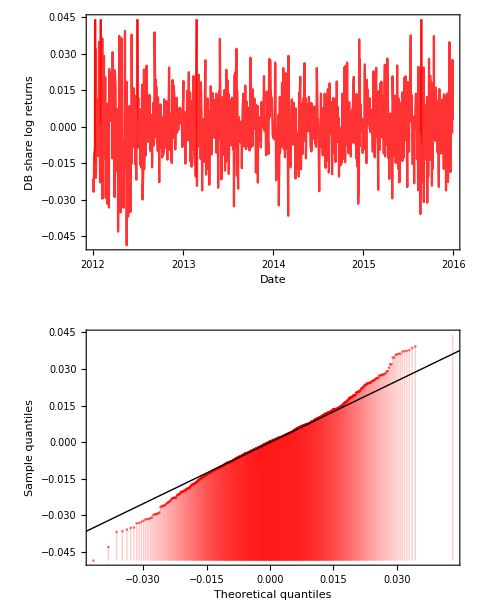

Figure Figure. Deutsche Boerse share returns exhibiting clustering and heavy tails in the observed range of  five and a half years.

Looking at the upper graph from Figure 13 periods of high followed by low volatility clusters are easily observable. Although nearly symmetric with skewness of 0.26 lower graph shows that empirical distribution is having fat tails in compare to normal, thus extreme events are more probable in compare to normal distributional assumption, also the density of points around the mean is higher than one would expected from normal distribution, contributing to 4.67 kurtosis.

We will fit three models from GARCH family previously described (here we are considering EWMA as a special case of GARCH) and discuss the results, the code will be shown in this case. In all three models we assume that unconditional mean of returns is 0, this assumption is justified by the fact that first moment of this time series is around 0.05%, a value that is indeed close to 0. Otherwise we would demean the time series or perhaps let Ugarch function estimate it along with other parameters.

We will start with GARCH(2, 2) model up to GARCH(1,0) and try to pick the one that fits the most by taking into account AIC or BIC information criteria and observing p values.

#### Section.Subsection.Subsubsection Model selection

Results from different information criteria are given in the Table 2 below. We are taking a shortcut here driven by empirical findings from practice. Mainly, in most cases scope of models based on lags higher than two have proven to be rarely statistically justified, see Hansen & Lunde (2001). In that sense we start from GARCH(2, 2) model downwards. It is highly  doubtable that conditional distributions will change ordering of models hence we presented only models with normal distribution of innovations (this statement is backed up by actually checking the results for Student t and generalized error distribution (from now on: GED) for given models in Table 2 and Table 3 ordering is identical).

Table TableTitle. Information criteria for selected GARCH models.

```mathematica
<<"garch`"
```

```mathematica
garchModels={"garch(2,2)","garch(2,1)","garch(1,2)","garch(1,1)","garch(2,0)","garch(1,0)"};AIC=Style[
TableForm[
Ugarch[dailyReturns,#,"infocriteria",Solver->"hybrid"][[1,All,1]]&/@garchModels,
TableHeadings->{garchModels,{"Akaike","Bayes","Shibata","Hannan-Quinn"}}],FontFamily->"Times New Roman"]
```

| Akaike | Bayes | Shibata | Hannan-Quinn
garch(2,2) | -5.86271 | -5.83835 | -5.86276 | -5.85346
garch(2,1) | -5.8612 | -5.84171 | -5.86123 | -5.85379
garch(1,2) | -5.86105 | -5.84156 | -5.86108 | -5.85364
garch(1,1) | -5.86391 | -5.84929 | -5.86392 | -5.85835
garch(2,0) | -5.81354 | -5.79893 | -5.81356 | -5.80799
garch(1,0) | -5.80103 | -5.79129 | -5.80104 | -5.79733

As suspected, GARCH(1, 1) is chosen as favorite model by all criteria, GARCH(2, 2) being the second best not counting BIC criteria which is more strict at penalizing number of parameters.

It should be noted that since one of the models had convergence issues we scaled the data by using Solver→”hybrid” option in Ugarch function, see appendix for more details of usage of this function from package.

We continue with analysing EGARCH model choice which is presented in Table 3.

Table 3. Information criteria for selected eGARCH models.

```mathematica
garchModels={"eGARCH(2,2)","eGARCH(2,1)","eGARCH(1,2)","eGARCH(1,1)","eGARCH(2,0)","eGARCH(1,0)"};
 AICe=Style[
TableForm[
Ugarch[dailyReturns,#,"infocriteria",ScaleModel->100,Solver->"hybrid"][[1,All,1]]&/@garchModels,
TableHeadings->{garchModels,{"Akaike","Bayes","Shibata","Hannan-Quinn"}}],FontFamily->"Times New Roman"]
```

| Akaike | Bayes | Shibata | Hannan-Quinn
eGARCH(2,2) | -5.87504 | -5.84093 | -5.87514 | -5.86209
eGARCH(2,1) | -5.87189 | -5.84265 | -5.87196 | -5.86078
eGARCH(1,2) | -5.87194 | -5.84757 | -5.87199 | -5.86268
eGARCH(1,1) | -5.87603 | -5.85654 | -5.87607 | -5.86863
eGARCH(2,0) | -5.811 | -5.78663 | -5.81104 | -5.80174
eGARCH(1,0) | -5.80041 | -5.78579 | -5.80043 | -5.79486

Table 3 shows results that are in line with ones from Table 1. It should be noted that here that criteria values are standardized by dividing true values with number of points.

We present the crucial part of code here which was used in making former two tables:

```mathematica
Ugarch[dailyReturns, model, "infocriteria", Solver->"hybrid"];
```

, where model stands for string given in the rows of the tables.  Going forward, code will be presented in same manner as here.

Although tempting to do the same for EWMA, one should recall that it is a special case of GARCH(1, 1) and it is against the nature derivation of that model to presented in section 4.4 to consider higher lags and log likelihood based measures, but indeed there exits a special variant of GARCH called iGARCH which could serve this purpose.

Going forward we calculate the coefficients for the above three selected models.

GARCH(1, 1) with normal, student t and generalized error distribution:

```mathematica
Ugarch[
dailyReturns,
"garch(1,1)",
ConditionalDistribution->#]&/@{"NormalDistribution",
"StudentTDistribution",
"Erf"}//Column;
```

Table 4. Estimation tables for GARCH(1, 1) model with Normal, Student t, generalized error conditional distributions of innovation term respectively.

|  Estimate |  Std. Error |  t value | Pr(>|t|)
omega | 2.37708×10^-6 | 1.88756×10^-6 | 1.25934 | 0.207907
alpha1 | 0.0370632 | 0.0106168 | 3.491 | 0.000481208
beta1 | 0.948923 | 0.0127365 | 74.504 | 0.
 |  Estimate |  Std. Error |  t value | Pr(>|t|)
omega | 3.31941×10^-6 | 2.86669×10^-6 | 1.15792 | 0.246896
alpha1 | 0.0422131 | 0.0134857 | 3.1302 | 0.00174685
beta1 | 0.93855 | 0.0173535 | 54.0841 | 0.
shape | 7.73842 | 1.81157 | 4.27167 | 0.0000194011
 |  Estimate |  Std. Error |  t value | Pr(>|t|)
omega | 2.85801×10^-6 | 2.87851×10^-6 | 0.992877 | 0.32077
alpha1 | 0.0386224 | 0.0134756 | 2.86611 | 0.00415549
beta1 | 0.944315 | 0.018019 | 52.4066 | 0.
shape | 1.43828 | 0.0931277 | 15.4442 | 0.

Note: Looking at the p values gives us reason to believe that we would perhaps consider EWMA as a  suitable replacement. Models with Student t and generalized error distribution have highly significant p values for shape parameters. In addition shape parameters of 5.6 in student t and 1.22 are clear evidence of fat tails and deviations from normality even with GARCH process.

All three models have significant alpha and beta coefficients implying existence of rather persistent volatility clustering. In addition heavy tails are evident looking how far are shape parameters from their value that would imply normality (∞ for Student t and 2 for GED).

eGARCH(1, 1) with normal Student t and generalized error distribution:

```mathematica
Ugarch[
dailyReturns,
"eGARCH(1,1)",
ConditionalDistribution->#]&/@{
"NormalDistribution",
"StudentTDistribution",
"Erf"}//Column;
```

Table 5. Estimation tables for eGARCH(1, 1) model with Normal, Student t, generalized error conditional distributions of innovation term respectively.

|  Estimate |  Std. Error |  t value | Pr(>|t|)
omega | -0.197663 | 0.00860534 | -22.9698 | 0.
alpha1 | -0.0572486 | 0.016527 | -3.46394 | 0.000532328
beta1 | 0.976604 | 0.000924742 | 1056.08 | 0.
gamma1 | 0.113154 | 0.00839959 | 13.4714 | 0.
 |  Estimate |  Std. Error |  t value | Pr(>|t|)
omega | -0.294518 | 0.0194074 | -15.1755 | 0.
alpha1 | -0.0647207 | 0.0210397 | -3.07612 | 0.00209716
beta1 | 0.965818 | 0.00219814 | 439.38 | 0.
gamma1 | 0.135542 | 0.0311059 | 4.35745 | 0.0000131587
shape | 8.41654 | 2.00324 | 4.20147 | 0.0000265186
 |  Estimate |  Std. Error |  t value | Pr(>|t|)
omega | -0.248651 | 0.0128719 | -19.3174 | 0.
alpha1 | -0.0608726 | 0.0201018 | -3.02821 | 0.00246009
beta1 | 0.971182 | 0.00149699 | 648.754 | 0.
gamma1 | 0.121494 | 0.0185209 | 6.55983 | 5.38682×10^-11
shape | 1.46805 | 0.0905977 | 16.2041 | 0.

Note: Results shown are in line with expectations in a sense that there is evidence of existing leverage effect. All parameters are highly significant.

Second and third subsection of Table 4 are showing clear evidence of leverage effect. Negative value of ARCH coefficient and positive value of leverage effect coefficient are in line with our expectations. Negative values of ARCH coefficient alpha1 and omega intercept are common in eGARCH model which contrary to GARCH does not impose positivity restrictions on coefficients. Shape parameters are close to those of GARCH model and significance of leverage gamma1 gives evidence of asymmetric correlation between returns and squared returns.

We will use a little trick here in order to calculate EWMA. Proposed value of λ=0.94 has proven to suit most of the practical use in risk management along with high p value for omega ω in previously evaluated GARCH(1, 1) model and value of beta1 coefficient that highly supports choosing λ=0.94, for the explanatory purpose we will still calculate λ as a special case of iGARCH(1, 1) with normal innovations. By iGARRCH here we mean a special case of GARCH with the constraint that ω+α+β=1. The estimated λ (beta1 in table) is presented in table 5, it's estimation is performed by setting ω to 0 in iGARCH model.

```mathematica
Ugarch[dailyReturns,"iGARCH(1,1)",FixedParameters->"omega=0"];
```

Table 6. EWMA estimated as iGARCH model with fixed value of parameter ω to 0.

|  Estimate |  Std. Error |  t value | Pr(>|t|)
omega | 0. | <NA> | <NA> | <NA>
alpha1 | 0.0360004 | 0.00749599 | 4.80262 | 1.56602×10^-6
beta1 | 0.964 | <NA> | <NA> | <NA>

Results from Table 5 give further evidence that rule of thumb λ value of 0.94 is reasonable choice when modeling Deutsche Boerse share returns volatility since beta1 coefficient is quite close to λ.

#### Section.Subsection.Subsubsection Residual analysis

As final filter before we enter models in backtest we are going to asses the fit of previous models. We concentrate on “eye techniques” here rather than using formal statistical tests mentioned in section. Nevertheless Ljung-Box test for serial autocorrelation of residuals and ARCH effects Lagrange multiplier test are available as a standard method for checking the residuals of the fit and they are part of the output of Ugarch function.

We start with GARCH models.

Figures 14, 15 and 16 are presented in order to asses how good is GARCH(1, 1) fitting daily Deutsche Boerse stock log returns. Figures present the output of Ugarch functions. Overall there exist 12 plots as an output but in order to preserve the pages we extracted 6 that are most interesting to us. Figures are representing GARCH(1, 1) with normal, Student t and GED distributions respectively.

ACF of standardized residuals and squared standardized residuals are presented in upper left and lower left part of graphs respectively. There are two spikes in serial autocorrelation of standardized residuals in all three models (remember that we did not model conditional mean here) which could be results of randomness of sample, according to Ruppert (2011), chapter 14 this is common in big samples. Interestingly all three distributions have succeeded to remove autocorrelation in squared returns implying that GARCH models are adequate in modeling this effect.

```mathematica
volatilityGarchNormal=Ugarch[dailyReturns,"garch(1,1)","quantile"][[1]]//Flatten;
volatilityGarchST=Ugarch[dailyReturns,"garch(1,1)","quantile",ConditionalDistribution->"StudentTDistribution"][[1]]//Flatten;
volatilityGarchGED=Ugarch[dailyReturns,"garch(1,1)","quantile",ConditionalDistribution->"Erf"][[1]]//Flatten;
BreachGarchNormal={dailyReturns[[All,1]],
dailyReturns[[All,2]],
volatilityGarchNormal}ᵀ;
BreachGarchST={dailyReturns[[All,1]],
dailyReturns[[All,2]],
volatilityGarchST}ᵀ;
BreachGarchGED={dailyReturns[[All,1]],
dailyReturns[[All,2]],
volatilityGarchGED}ᵀ;
FilterBreaches[data_]:=Module[{filter1,filter2},
filter1=Cases[data,{a_,b_,c_}/;(b<0)];
filter2=Cases[filter1,{a_,b_,c_}/;c>b]];
FilterBreaches[BreachGarchNormal];
FilterBreaches[BreachGarchST];
FilterBreaches[BreachGarchGED];
```

Upper middle plots are showing log returns series with 1%VaR superimposed. Observed numbers of 1%VaR breaches are 10 for Normal and 8 for  Student t and  GED. Thus we can claim that all three models are satisfactory from this perspective although Student t and GED seem to perform better. Absolute returns with conditional volatility are shown in lower middle graphs.

Finally, looking at the right plots shortcomings of normal distributional assumptions are obvious, log returns cluster around mean more than one would expect from normal distribution given kurtosis of 4.67. Quantile plot of normal conditional residuals shows the presence of heavy tails. Situation is much better with Student t and GED, it seems that Student t residuals are marginally better in fitting whole range but also GED shows marginal improvement in lower tail in which we are concerned the most since it is closer to the last three residuals.

In general we would opt for either one of the Student t or GED.

```mathematica
GarchNormalGraphs=Ugarch[dailyReturns,"garch(1,1)","plot"];
Partition[
GarchNormalGraphs[[1,1,All,2]][[{10,2,8,11,3,9}]],
3]//GraphicsGrid;
```

-Graphics-

Figure Figure. The daily  Deutsche Boerse stock log returns series sample ACF of the standardized conditional residuals/up and standardized squared residuals from GARCH(1, 1) with normal distribution assumption/down;  log return series with corresponding 1% VAR of estimated conditional volatilities superimposed/up and estimated conditional volatility against  absolute value of log return series/down; empirical density histogram of standardized residuals against theoretical normal distribution density/up  and quantile plot of standardized residuals/down.

```mathematica
GarchSTGraphs=Ugarch[dailyReturns,"garch(1,1)","plot",ConditionalDistribution->"StudentTDistribution"];
Partition[
GarchSTGraphs[[1,1,All,2]][[{10,2,8,11,3,9}]],
3]//GraphicsGrid;
```

-Graphics-

Figure Figure. The daily  Deutsche Boerse stock log returns series sample ACF of the standardized conditional residuals/up and standardized squared residuals from GARCH(1, 1) with Student t distribution assumption;down;  log return series with corresponding 1% VAR of estimated conditional volatilities superimposed/up and estimated conditional volatility against  absolute value of log return series/down; empirical density histogram of standardized residuals against theoretical Student t distribution density/up  and quantile plot of standardized residuals/down.

```mathematica
GarchGEDGraphs=Ugarch[dailyReturns,"garch(1,1)","plot",ConditionalDistribution->"Erf"];
Partition[
GarchGEDGraphs[[1,1,All,2]][[{10,2,8,11,3,9}]],
3]//GraphicsGrid;
```

-Graphics-

Figure Figure. The daily  Deutsche Boerse stock log returns series sample ACF of the standardized conditional residuals/up and standardized squared residuals from GARCH(1, 1) with generalized error distribution assumption/down;  log return series with corresponding 1% VAR of estimated conditional volatilities superimposed/up and estimated conditional volatility against  absolute value of log return series/down; empirical density histogram of standardized residuals against theoretical generalized error distribution density/up  and quantile plot of standardized residuals/down.

We will now asses fit of eGARCH(1, 1) models by discussing figures 17, 18 and 19. The order of distributions is following that of GARCH(1, 1). Including the leverage effect does improve the fit. Namely number of times that 1%VaR was breached for normal distribution is 9, for Student t and GED this number lower even more, it’s 6. Thus, the leverage effect is successful at capturing this asymmetry in volatility.

We would expect on average this number of exceedances to be around 10. From perspective of VaR framework every single model considered here would be acceptable looking just at the number of times we expect loses to exceed 1%VaR threshold, however a previously described shortcoming of VaR in a modern risk perspective is obvious here. If we were to rely on normal distribution we would be underestimating the magnitude of unexpected losses when they came, i.e. although unexpected losses would happen with expected frequency, their magnitude would be on average more extreme than one would expect from left tail of normal distribution.

On the other hand, looking at the quantile plots with Student t and GED we would be quite close in our “ranking” of looses, even more, it seems that we would overestimate them a little (as in simple GARCH case).

To conclude, normal distribution is a performing the worst from risk perspective here, although number of exceedances is acceptable with expectations, fat tails still exist in either GARCH and eGARCH.

Other two distributions are good in capturing non normality and fat tails, they are even a little conservative. The differences between Student t and GED are marginal, like in GARCH(1, 1) case, although the returns are better fitted by Student t overall, GED is marginally better in lower tail of distribution where Student t is more conservative by a margin.

Both models are exhibiting two positive spikes, here we did not pay much attention to them since we are mainly concerned with lower tail, however this will lead, as we will see in next section, for symmetrical models to outperform asymmetrical ones due to larger adjustment. The model is good as much as his assumptions are close to reality.

```mathematica
volatilityeGarchNormal=Ugarch[dailyReturns,"eGARCH(1,1)","quantile"][[1]]//Flatten;
volatilityeGarchST=Ugarch[dailyReturns,"eGARCH(1,1)","quantile",ConditionalDistribution->"StudentTDistribution"][[1]]//Flatten;
volatilityeGarchGED=Ugarch[dailyReturns,"eGARCH(1,1)","quantile",ConditionalDistribution->"Erf"][[1]]//Flatten;
BreacheGarchNormal={dailyReturns[[All,1]],
dailyReturns[[All,2]],
volatilityeGarchNormal}ᵀ;
BreacheGarchST={dailyReturns[[All,1]],
dailyReturns[[All,2]],
volatilityeGarchST}ᵀ;
BreacheGarchGED={dailyReturns[[All,1]],
dailyReturns[[All,2]],
volatilityeGarchGED}ᵀ;
FilterBreaches[data_]:=Module[{filter1,filter2},
filter1=Cases[data,{a_,b_,c_}/;(b<0)];
filter2=Cases[filter1,{a_,b_,c_}/;c>b]];
FilterBreaches[BreacheGarchNormal];
FilterBreaches[BreacheGarchST];
FilterBreaches[BreacheGarchGED];
```

In next subsection we will test number of exceedances on validation sample from beginning to an end of 2016, totaling around 250 observations.

```mathematica
eGarchNormalGraphs=Ugarch[
dailyReturns,"eGARCH(1,1)",
"plot"];
Partition[
eGarchNormalGraphs[[1,1,All,2]][[{10,2,8,11,3,9}]],
3]//GraphicsGrid;
```

-Graphics-

Figure Figure. The daily  Deutsche Boerse stock log returns series sample ACF of the standardized conditional residuals/up and standardized squared residuals from eGARCH(1, 1) with normal distribution assumption/down;  log return series with corresponding 1% VAR of estimated conditional volatilities superimposed/up and estimated conditional volatility against  absolute value of log return series/down; empirical density histogram of standardized residuals against theoretical normal distribution density/up  and quantile plot of standardized residuals/down.

```mathematica
eGarchSTGraphs=Ugarch[
dailyReturns,"eGARCH(1,1)",
"plot",ConditionalDistribution->"StudentTDistribution"];
Partition[
eGarchSTGraphs[[1,1,All,2]][[{10,2,8,11,3,9}]],
3]//GraphicsGrid;
```

-Graphics-

Figure Figure. The daily  Deutsche Boerse stock log returns series sample ACF of the standardized conditional residuals/up and standardized squared residuals from eGARCH(1, 1) with Student t distribution assumption;down;  log return series with corresponding 1% VAR of estimated conditional volatilities superimposed/up and estimated conditional volatility against  absolute value of log return series/down; empirical density histogram of standardized residuals against theoretical Student t distribution density/up  and quantile plot of standardized residuals/down.

```mathematica
GarchGEDGraphs=Ugarch[
dailyReturns,"garch(1,1)",
"plot",ConditionalDistribution->"Erf"];
Partition[
GarchGEDGraphs[[1,1,All,2]][[{10,2,8,11,3,9}]],
3]//GraphicsGrid;
```

-Graphics-

Figure Figure. The daily  Deutsche Boerse stock log returns series sample ACF of the standardized conditional residuals/up and standardized squared residuals from eGARCH(1, 1) with generalized error distribution assumption/down;  log return series with corresponding 1% VAR of estimated conditional volatilities superimposed/up and estimated conditional volatility against  absolute value of log return series/down; empirical density histogram of standardized residuals against theoretical generalized error distribution density/up  and quantile plot of standardized residuals/down.

Finally, we evaluate EWMA as a iGARCH model from Ugarch function with fixed parameter beta to 0.94 and omega to 0. As expected it performs similar to GARCH(1, 1) model with normal conditional innovations. Exception is one statistically significant spike in ACF of squared residuals on forth lag. For convenience we replaced upper right graph in order to trace this serial autocorrelation in squared log returns.

In addition there are 11 exceedances of 1%VaR in, which is in line with what we would expect from 1000 observations.

```mathematica
volatilityEWMA=Ugarch[dailyReturns,"iGARCH(1,1)","quantile",
FixedParameters->"beta1=0.94,omega=0"][[1]]//Flatten;
BreacheEWMA={dailyReturns[[All,1]],
dailyReturns[[All,2]],
volatilityEWMA}ᵀ;
FilterBreaches[BreacheEWMA]//Grid
```

{2012,4,12} | -0.0430871 | -0.038749
{2012,5,17} | -0.0486871 | -0.045248
{2013,7,26} | -0.0327146 | -0.0271698
{2014,1,24} | -0.03228 | -0.027289
{2014,3,3} | -0.0365679 | -0.0268697
{2014,7,7} | -0.0264723 | -0.0203539
{2014,12,12} | -0.0316564 | -0.0231177
{2015,3,3} | -0.0258993 | -0.0256228
{2015,4,29} | -0.0294412 | -0.0260543
{2015,8,20} | -0.0316867 | -0.0305115
{2015,8,21} | -0.0358875 | -0.0330614

```mathematica
EWMAGraphs=Ugarch[
dailyReturns,"iGARCH(1,1)",
"plot",
FixedParameters->"beta1=0.94,omega=0"];
Partition[
EWMAGraphs[[1,1,All,2]][[{10,2,5,11,3,9}]],
3]//GraphicsGrid
```

-Graphics-

Figure Figure. The daily  Deutsche Boerse stock log returns series sample ACF of the standardized conditional residuals/up and standardized squared residuals from EWMA /down;  log return series with corresponding 1% VAR of estimated conditional volatilities superimposed/up and estimated conditional volatility against  absolute value of log return series/down; empirical  ACF of squared Deutsche Boerse stock log returns/up  and quantile plot of standardized residuals/down.

#### Section.Subsection.Subsubsection Backtesting GARCH based models

In order to asses how well previously discussed models behave out of sample we will use a backtest on testing sample that dates from the beginning of 2016. As before VaR^(1%) will be considered in order to stay.

We explore results and apply two formal statistical tests described earlier in this thesis, in particular, unconditional coverage test and independence test.

Estimation window is set to 1000 observations before the year of 2016 which is almost all the data that were used in previous subsection. Models are refitted daily and one day VaR^(1%) forecasts are collected into vector in order to count number of exceedances and their magnitude.

The function that was exploited in this section is UgarchForcast. It was wrapped in Mathematica code in order to make sliding predictions of models. The relevant part of code is given below:

```mathematica
Options[backtest]={FixedParameters->""};
backtest[
ret_,Nrolls_,
Windowlength_, 
model_String,
garchDistribution_String,
opts:OptionsPattern[]]:=Module[
{nrolls=Nrolls,windowlength=Windowlength,T1,T2,
slider,T,from,to,by,celideo,ostatak,provera,
rezultat,Model=model,distribution=garchDistribution},
T=ret//Length;
from=windowlength;
to=T-(nrolls+1);
by=nrolls+1;
celideo=Table[
T1=t-windowlength+1;
T2=t+nrolls;
slider=ret[[T1;;T2,All]];
(******UgarchForecast function***********)
UgarchForecast[
Ugarch[slider,Model,Solver->"hybrid",
OutSample->nrolls, 
ConditionalDistribution->distribution,
FixedParameters->OptionValue[FixedParameters]],
"quantile",1,nrolls][[1,1]],{t,from,to,by}
];
(**************************************)
provera=Mod[(T-windowlength),nrolls+1];
If[
provera≠0,T2=T2+1;T1=T2-windowlength+1;slider=ret[[T1;;T2,All]];ostatak=UgarchForecast[Ugarch[slider,"garch(1,1)",Solver->"hybrid",OutSample->(provera-1), ConditionalDistribution->distribution,FixedParameters->OptionValue[FixedParameters]],"quantile",1,provera-1][[1,1]];

];
If[provera≠0,rezultat={Flatten@celideo,Flatten@ostatak}//Flatten,rezultat=Flatten@celideo];
rezultat
]
```

```mathematica
resultGarchNormal=backtest[dailyReturnsTest,0,1000,"garch(1,1)","NormalDistribution"];
```

```mathematica
resultGarchST=backtest[dailyReturnsTest,0,1000,"garch(1,1)","StudentTDistribution"];
```

```mathematica
resultGarchGED=backtest[dailyReturnsTest,0,1000,"garch(1,1)","Erf"];
```

```mathematica
resulteGarchNormal=backtest[dailyReturnsTest,0,1000,"eGARCH(1,1)","NormalDistribution"];
```

```mathematica
resulteGarchST=backtest[dailyReturnsTest,0,1000,"eGARCH(1,1)","StudentTDistribution"];
```

```mathematica
resulteGarchGED=backtest[dailyReturnsTest,0,1000,"eGARCH(1,1)","Erf"];
```

```mathematica
resultEWMA=backtest[dailyReturnsTest,0,1000,"iGARCH(1,1)","NormalDistribution",FixedParameters->"omega=0,beta1=0.94"];
```

```mathematica
BreacheEWMAB={dailyReturnsTest[[1010;;All,1]],
dailyReturnsTest[[1010;;All,2]],
resultEWMA[[10;;All]]}ᵀ;
FilterBreaches[BreacheEWMAB]
Total[FilterBreaches[BreacheEWMAB][[All,2]]-FilterBreaches[BreacheEWMAB][[All,3]]]
```

{{{2016,1,4},-0.0377576,-0.034312},{{2016,4,29},-0.031279,-0.0272478},{{2016,6,24},-0.0858297,-0.0336852},{{2016,9,30},-0.0211455,-0.0211227}}

-0.0596441

```mathematica
BreachGarchNormalB={dailyReturnsTest[[1010;;All,1]],
dailyReturnsTest[[1010;;All,2]],
resultGarchNormal[[10;;All]]}ᵀ;
FilterBreaches[BreachGarchNormalB]
Total[FilterBreaches[BreachGarchNormalB][[All,2]]-FilterBreaches[BreachGarchNormalB][[All,3]]]
```

{{{2016,1,4},-0.0377576,-0.0336747},{{2016,4,29},-0.031279,-0.0247688},{{2016,6,24},-0.0858297,-0.0370142},{{2016,12,1},-0.023504,-0.0223366}}

-0.0605759

```mathematica
FilterBreaches[data_]:=Module[{filter1,filter2},
filter1=Cases[data,{a_,b_,c_}/;(b<0)];
filter2=Cases[filter1,{a_,b_,c_}/;c>b]];
BreachGarchSTB={dailyReturnsTest[[1010;;All,1]],
dailyReturnsTest[[1010;;All,2]],
resultGarchST[[10;;All]]}ᵀ;
FilterBreaches[BreachGarchSTB]
Total[FilterBreaches[BreachGarchSTB][[All,2]]-FilterBreaches[BreachGarchSTB][[All,3]]]
```

{{{2016,1,4},-0.0377576,-0.0368281},{{2016,4,29},-0.031279,-0.0267588},{{2016,6,24},-0.0858297,-0.0399779}}

-0.0513015

```mathematica
BreachGarchGEDB= {dailyReturnsTest[[1010 ;; All, 1]],
    dailyReturnsTest[[1010 ;; All, 2]],
    resultGarchGED[[10 ;; All]]}ᵀ;
FilterBreaches[BreachGarchGEDB]
Total[FilterBreaches[BreachGarchGEDB][[All,2]]-FilterBreaches[BreachGarchGEDB][[All,3]]]
```

{{{2016,1,4},-0.0377576,-0.036577},{{2016,4,29},-0.031279,-0.0268145},{{2016,6,24},-0.0858297,-0.0400044}}

-0.0514703

```mathematica
BreacheGarchNormal= {dailyReturnsTest[[1010 ;; All, 1]],
    dailyReturnsTest[[1010 ;; All, 2]],
    resulteGarchNormal[[10 ;; All]]}ᵀ;
FilterBreaches[BreacheGarchNormal]
Total[FilterBreaches[BreacheGarchNormal][[All,2]]-FilterBreaches[BreacheGarchNormal][[All,3]]]
```

{{{2016,1,4},-0.0377576,-0.033729},{{2016,4,29},-0.031279,-0.0248397},{{2016,6,24},-0.0858297,-0.029948},{{2016,8,22},-0.0224226,-0.0215417},{{2016,12,1},-0.023504,-0.019833}}

-0.0709014

```mathematica
BreacheGarchST= {dailyReturnsTest[[1010 ;; All, 1]],
    dailyReturnsTest[[1010 ;; All, 2]],
    resulteGarchST[[10 ;; All]]}ᵀ;
FilterBreaches[BreacheGarchST] 
Total[FilterBreaches[BreacheGarchST][[All,2]]-FilterBreaches[BreacheGarchST][[All,3]]]
```

{{{2016,1,4},-0.0377576,-0.0355993},{{2016,4,29},-0.031279,-0.0266993},{{2016,6,24},-0.0858297,-0.0323391},{{2016,12,1},-0.023504,-0.0223409}}

-0.0613916

```mathematica
BreacheGarchGED= {dailyReturnsTest[[1010 ;; All, 1]],
    dailyReturnsTest[[1010 ;; All, 2]],
    resulteGarchGED[[10 ;; All]]}ᵀ;
FilterBreaches[BreacheGarchGED] 
Total[FilterBreaches[BreacheGarchGED][[All,2]]-FilterBreaches[BreacheGarchGED][[All,3]]]
```

{{{2016,1,4},-0.0377576,-0.0360242},{{2016,4,29},-0.031279,-0.0268134},{{2016,6,24},-0.0858297,-0.0322171},{{2016,12,1},-0.023504,-0.0219586}}

-0.0613569

Having only 250 observations certainly effects the power of our test (given that we are considering VaR^(1%)), and one should consider longer horizons in order to get any meaningful results. I

```mathematica
IndipendenceTest[T_Integer,violations_Integer,p_Real]:=Module[{Lhat,L,phat=violations/T,LR,pvalue},
Lhat=(1-phat)^(T-violations) phat^violations;
L=(1-p)^(T-violations) p^violations;
LR=-2 (Log[L/Lhat]);
pvalue=1-CDF[ChiSquareDistribution[1],LR];
{LR,pvalue}
];IndipendenceTest[258,5,0.01];
```

Table 7. Number of exceedances and coverage test of models considered

Distribution | Model | 4/1/16 | 29/4/16 | 24/6/16 | 22/8/16 | 30/9/16 | 1/12/16 | Statistic | p value
Normal | GARCH | + | + | + | + | - | - | 0.676 | 0.412
 | eGARCH | + | + | + | + | - | + | 1.799 | 0.180
Student t | GARCH | + | + | + | - | - | - | 0.066 | 0.798
 | eGARCH | + | + | + | - | - | + | 0.676 | 0.412
Gen. error | GARCH | + | + | + | - | - | - | 0.066 | 0.798
 | eGARCH | + | + | + | - | - | + | 0.676 | 0.412
EWMA |  | + | + | + | - | + | - | 0.676 | 0.412

Note: Clearly, looking at dates of exceedances applying independence test would not be of importance here.

Clearly, given the sample size presented results are merely a guidance, Danielsson (2011) suggests that in order to coverage test function properly in the means of its power in a sample of 250 observations we would need at least 10 exceedances. In this context, repeating the procedure with 5%VaR or even 10%VaR in order to make a decision which model is satisfactory for us is definitely the way to go, and this is easily doable with the code provided, however this statement stays as it is, a recommendation, given the nature of this section is conceptual rather than empirical.

Although, no statistically significant differences can happen between models considered in small sample like this, and we could easily justifiable pick any model presented, still  surprisingly GARCH models outperformed eGARCH. Models with normal distribution performed the worse, both GARCH and EWMA had 4 hits against 5 of eGARCH. Although eGARCH improved with two other distribution, it did not succeed to adjust to spike at the beginning of December. The most surprising is that EWMA is holding its ground to more sophisticated GARCH and eGARCH, in fact the exceedance in September is marginal.

If we were to pick one model we could sum up the overall sum of exceedances in order to pick a model with lowest sum among the ones that exhibited lowest number of hits. Since here there is no statistically statistical difference between models we opted for this solution, although as mentioned before, looking at the different VaR measures is more suiting way to deal with this issue. Another solution from the institutional perspective would be to pick a model that minimizes Basel market risk formula in equation  (92).

In this context we pick GARCH(1, 1) model with Student t which performs slightly better than the one with generalized error distribution (-0.0515 vs -0.0513). Interestingly enough EWMA outperforms normal GARCH and eGARCH in this contest, although the difference is marginal in compare to normal GARCH(1, 1).

However structural breaks like the one on the day after Brexit could not be predicted by neither of models.

```mathematica
eGARCHHitGED={{-0.037757625593942024,-0.03602422033886934},{-0.03127896585212753,-0.02681339126319406},{-0.08582967578374312,-0.0322170986658716},{-0.02350396048580805,-0.021958638886649732}};
Total[eGARCHHitGED[[All,1]]-eGARCHHitGED[[All,2]]]
```

-0.0613569

```mathematica
eGARCHHitST={{-0.037757625593942024,-0.03559933063252899},{-0.03127896585212753,-0.026699279843825863},{-0.08582967578374312,-0.032339104005136794},{-0.02350396048580805,-0.022340932660597647}};
Total[eGARCHHitST[[All,1]]-eGARCHHitST[[All,2]]]
```

-0.0613916

```mathematica
eGARCHHitN={{-0.037757625593942024,-0.03372898290559699},{-0.03127896585212753,-0.024839734593527132},{-0.08582967578374312,-0.029948035991467538},{-0.022422592646840656,-0.021541704657574327},{-0.02350396048580805,-0.019832952607149578}};
Total[eGARCHHitN[[All,1]]-eGARCHHitN[[All,2]]]
```

-0.0709014

```mathematica
GarchHitGED={{-0.037757625593942024,-0.03657698567492936},{-0.03127896585212753,-0.026814515520563055},{-0.08582967578374312,-0.04000444021810641}};
Total[GarchHitGED[[All,1]]-GarchHitGED[[All,2]]]
```

-0.0514703

```mathematica
GarchHitST={{-0.037757625593942024,-0.03682811577681436},{-0.03127896585212753,-0.02675875093349312},{-0.08582967578374312,-0.03997785118997748}};
Total[GarchHitST[[All,1]]-GarchHitST[[All,2]]]
```

-0.0513015

```mathematica
GarchHitN={{-0.037757625593942024,-0.03367469777206686},{-0.03127896585212753,-0.024768780352253966},{-0.08582967578374312,-0.037014213268346974},{-0.02350396048580805,-0.022336620876265187}};
Total[GarchHitN[[All,1]]-GarchHitN[[All,2]]]
```

-0.0605759

```mathematica
EwmaHit={{-0.037757625593942024,-0.03431201385818854},{-0.03127896585212753,-0.027247753871877757},{-0.08582967578374312,-0.0336852363053431},{-0.02114551991497926,-0.021122690804480634}};
Total[EwmaHit[[All,1]]-EwmaHit[[All,2]]]
```

-0.0596441

Finally, it is always preferable to plot the results, hence we present the graph of the winning model from backtesting procedure.

```mathematica
seriesAndDates={dailyReturnsTest[[1010 ;; All, 1]],
    dailyReturnsTest[[1010 ;; All, 2]]}ᵀ;
```

```mathematica
resultAndDates={dailyReturnsTest[[1010 ;; All, 1]],
    resultGarchST[[10 ;; All]]}ᵀ;
```

```mathematica
extremesAndDates=FilterBreaches[BreachGarchSTB][[All,{1,2}]];
```

```mathematica
(*function for finding indexes of returns smaller than VaR*)

DateListPlot[{resultAndDates,seriesAndDates},ImageSize->Large,Joined->{True,False},PlotLegends->Placed[SwatchLegend[{Black,Red,Orange},Style[#,10,FontFamily->"Times New Roman"]&/@{"1% VaR GARCH ST","Series","Series Excess points"}],Top],PlotStyle->{{Black},{Red}},Filling->{{1->Axis},{2->Axis}},PlotTheme->"Detailed",Epilog->{PointSize->.0125,Orange,Point[extremesAndDates]},FrameLabel->{"Dates, 2016","VaR and series"}]
```

-Graphics-

Figure Figure. Graph of winner model GARCH(1, 1) with Student t distributions of conditional innovation. All excess point are happening before July of 2016.

### Section.Subsection Calculating liquidity adjusted VaR measure

In first subsection we will present calculation of LVaR measure using GARCH(1, 1) model with Student t distribution from previous section for quantifying daily market price risk and time series of relative bid/ask quotes. We will calculate VaR^(1%) of relative bid/ask quotes as an quantile of their empirical distribution. In a sense we use historical simulation method on relative bid/ask spread. In order to get actual bid/ask spread VaR, relative spread VaR must be multiplied by value under VaR first. Finally we add the GARCH calculated price VaR and bid/ask spread in order to get LVaR.

In second subsection we deal with special case where bid/ask date are not available but we have intraday prices. We propose a solution of calculating daily relative bid/ask spread from those available intraday prices using Rolls measure. One example of place where free intraday prices can be obtained for variety of stocks is the Bonnot Gang site. Implied spread was calculated in three different frequencies and compared to quoted spread at the end of the day and average quoted spread during the day. Frequencies used were 1, 5 and 15 minutes. Tho former described methods in calculating implied measure of spread were applied, namely, moment based and Gibbs based method.

Conclusions were drawn.

#### Section.Subsection.Subsubsection LVaR using end of the day quotes

In order to incorporate liquidity risk into VaR framework we will conceptually follow Bangia et al. (2002), although criticized for its simplifying assumptions about correlation of market price risk and liquidity risk which is assumed to be 1 in tails, Bangia et al. (2002) approach is still one of the most natural and easy to apply in practice. Although assumption of perfect correlation have been empirically tested, criticized and different solutions have been proposed as a way of overcoming them in academic papers, most of the solution are requiring large scale of daily and even intraday data. See for example Stange & Kaserer ( 2010), or Saout (2002). Even though their models are more advanced, they are using data which is hardly obtainable. Nevertheless, we will incorporate some correction in Bangia et al. (2002) paper in next section.

In its essence Bangia et al. (2002) are modeling risk born from cost of liquidation at the end of the day that we need to pay since in conventional market risk framework we assumed no friction in trading.

In addition instead of calculating theirs heavy tail correction parameter, we opted for empirical quantile here as is more natural and also less data hungry given that we are dealing only with one stock. Thus, we apply historical simulation method in order to calculate relative bid/ask spread VaR.

Empirical distributions of bid/ask spread data are, naturally, bounded by 0 in the left tail, thus making their distribution right skewed. In addition, they are often multimodal with heavy and long right tails. All fore-mentioned is making bid/ask data inconvenient to model with parametric families of distributions.

```mathematica
dailyRelativeBidAsk = {rawData[[3 ;; All, 1, 1]], rawData[[3 ;; All, 13]]}ᵀ[[1;;1009]];
BidAskHist=SmoothHistogram[dailyRelativeBidAsk[[All,2]],
PlotRange->{{-0.0001,0.004},{0,2000}},(*PlotRange->{{0,0.022},{0,1200}},*)
Filling->Axis,FillingStyle->Directive[Opacity[.4],Red],
Frame->{True,True,False,False},
FrameLabel->{"Relative Bid/Ask spread","Density"},FrameStyle->Directive[FontFamily->"Times New Roman",Black,10]
,PlotStyle->Directive[Thick,Black]
]
```

-Graphics-

Figure Figure. Empirical smooth histogram of end of day Deutsche Boerse stock relative bid/ask spread from 2012 until the end of 2015.

Figure Figure shows that end of day Deutsche Boerse stock relative bid/ask spread is no exception to former mentioned behavior. It is heavily skewed to the right, with heavy right tails (kurtosis of 178, see Table 8), also, it has two modes around the median, see Table 8.

```mathematica
descriptive1=TraditionalForm@TableForm[Round[{{Mean[#],StandardDeviation[#],Min[#],Max[#],Median[#]}},0.0001],
TableHeadings->{{},{"Average","St. deviation","Min","Max","   Median"}}
]&@@{dailyRelativeBidAsk[[All,2]]  }
descriptive2=TraditionalForm@TableForm[
Round[{
{Skewness[#],Kurtosis[#],Quantile[#,0.25],Quantile[#,0.75],Quantile[#,99/100]}},{{0.001,0.01,0.0001,0.0001,0.0001}}],
TableHeadings->{{},{"Skewnes","Kurtosis      ","1^stQ","3^rd  Q","99^th perc."}}
]&@@{dailyRelativeBidAsk[[All,2]]  }
```

Table TableTitle. End of day Deutsche Boerse stock relative bid/ask spread descriptive statistics in % of mid price.

| Average | St. deviation | Min | Max |    Median
 | 0.0684 | 0.0941 | 0.0082 | 1.8735 | 0.0563

| Skewnes | Kurtosis       | 1^stQ | 3^rd  Q | 99^th perc.
 | 11.521 | 179.16 | 0.0418 | 0.0728 | 0.4267

Other assumption that needs to be taken with caution is perfect tail correlation assumption. In fact, this is the biggest defiance of Bangia et al. (2002) approach and it is being overly criticized in papers. Most of the papers do not find empirical evidence of perfect tail correlation, see Stange & Kaserer (2009, 2010), Ernst, Stange, & Kaserer (2009). Two useful approaches that they provide are Cornish-Fisher approximation to determine percentiles instead of using them from historical distribution and avoiding perfect correlation assumption by modeling returns net of liquidity cost thus working with one instead of two distributions.

```mathematica
returnsq={rawData[[3 ;; All, 1, 1]], rawData[[3 ;; All, {14,13}]]}ᵀ;
extremeReturns[DatesandReturnsandSpread_,
column_Integer,quant_Real]:=Select[DatesandReturnsandSpread,#[[2,column]]≤Quantile[DatesandReturnsandSpread[[All,2,column]],quant]&];
VaRCorrelations=Correlation[
extremeReturns[returnsq,1,#][[All,2,1]],
extremeReturns[returnsq,1,#][[All,2,2]]]&/@{0.1,0.05,0.025,0.01,0.005};
Style[TableForm[{VaRCorrelations},TableHeadings->{{},{"10%","5%","2.5%","1%","0.5%"}}],FontFamily->"Times New Roman"];
```

All above being stated, we proceed calculating $LVaR by applying equation (EquationNumbered). We estimated log return VaR^(1%) for the first working day of 2017 using GARCH(1, 1) with Student t conditional innovations on last 1000 trading days to be 0.0254 and using historical simulation we estimated 99% quantile to be (for same 1000 observations) 0.0031. Replacing these values in equations (EquationNumbered), (EquationNumbered) and knowing the price at 12/30/2016 was 87.845 gives us liquidity adjusted $VaR:

```mathematica
<<"garch`"
returns2017=dailyReturnsTest[[(Length[dailyReturnsTest]-999);;All]];
VaR2017=UgarchForecast[Ugarch[returns2017,"garch(1,1)",ConditionalDistribution->"StudentTDistribution"],"quantile",1,0][[1,1,1]];
Bid2017Raw=rawData[[3;;1269,{1,13}]][[(Length[dailyReturnsTest]-999);;All]];
Bid2017Raw1=rawData[[3;;1269,{1,13}]];
Bid2017={Bid2017Raw[[All, 1, 1]],Bid2017Raw[[All, 2]]}ᵀ;
Bid20171={Bid2017Raw[[All, 1, 1]],Bid2017Raw[[All, 2]]}ᵀ;
VaRL2017=Quantile[Bid2017[[All,2]],0.99];
VaRL20171=Quantile[Bid20171[[All,2]],0.99];
priceEnd2016=rawData[[1269,14]];
LVaR[price_,pVaR_,BidAskVaR_]:=price(1-ⅇ^-pVaR+ⅇ^-pVaR 1/2 BidAskVaR);
LVaR[priceEnd2016,-VaR2017,VaRL2017];
percentageOfLrisk=priceEnd2016 ⅇ^VaR2017 1/2 VaRL2017/LVaR[priceEnd2016,-VaR2017,VaRL2017];
```

$LVaR=87.845(1- ⅇ^(-.0254))+1/2 87.845 ⅇ^(-.0254)·0.0031=2.33318

, where liquidity risk is representing 5.68% of total risk. Despite the fact that, indeed, 5.68% is not a big share of total risk, which is to some extent expected given that Deutsche Boerse is member of DAX 30 and that is highly liquid, for lower liquidity stocks liquidity risk can share up to 50% of overall risk, for example see Saout (2002) and Lei & Lai (2007). Bangia et al. (2002) finds that risk is underestimated by 20%-30% in emerging market currencies.

#### Section.Subsection.Subsubsection Calculating Roll’s implied spread in absence of bid ask data

Bid/ask spread data may not always be available, if such case occurs one possible solution that can be applied is to calculate implied spread by applying equation (EquationNumbered) to intraday returns if available.

In order to show results from such a calculation we estimated implied spread by applying moment based and Gibbs based estimator.

Data used in calculation dates from June of 2015 and was downloaded from the site of Dukascopy Bank SA. We will be violating homogeneity of sample mainly because we used 1000 data points for historical simulation of cost of liquidation VaR but we have obtained only year and a half of intraday data in that date range. Data is covering trading hours on Xetra from Mondays to Fridays from 9 a.m. until 5.30 p.m. CET.

Data was adjusted for a dividend payout at May, 12 2016. In general, adjusting intraday data for dividends is a complicated issue that has not been addressed properly in academic literature yet, even more, there are contradictory findings of speed of adjustment of intraday prices over different markets, see Vinaja (2009) and seminal work of Patell & Wolfson (1984), but given that payout happened off trading hours we adjusted prices the usual way.

Three different frequencies have been considered, namely 1, 5 and 15 minutes for moment based estimator. Results were then compared with daily average and closing bid/ask spread. For the frequency of data whose estimator was closest to true one Gibbs estimator was rerun. Moment based daily estimators were compared to the true ones by means of first two moments and correlation.

Patterns in intraday spreads have been extensively described in literature, for example see for Yan & Zivot (2003) for a practical guidance.

Our data is no different, Figure FigureCaption shows that there is a clear pattern in spread during the day governed by opening, closing and intraday auction at 1pm. It can be seen that opening spread is twice as high than the one at 1pm and the closing one. We observe reverse J pattern rather than U shaped one.

```mathematica
avrgHourlySpread = Import[StringReplace[(NotebookDirectory[] <> "AvrhHourlySpread.xlsx"), "\\" -> "/"], "XLSX"][[1,2;;All]];
DateListPlot[avrgHourlySpread,
PlotRange->{{avrgHourlySpread[[1,1]],avrgHourlySpread[[-1,1]]+LinguisticAssistant},{0.0004,0.003}},
PlotStyle -> Directive[Opacity[.8], Red],
   FrameLabel -> {"Date", "DB share average 1 minute spread"},
   FrameStyle -> Directive[FontFamily -> "Times New Roman", Black, 10],
   FrameTicks -> {{Automatic, None}, {Automatic, None}},
   GridLines -> Automatic, GridLinesStyle -> Directive[Black, Dashed],
ImageMargins->0,Filling->Axis]
```

-Graphics-

Figure Figure. Daily pattern of Deutsche Boerse stock relative bid/ask spread. One minute averages over two years of data (June, 2015 - June, 2017) are shown.

Removing intraday auction observations did not make any meaningful difference in results which can be expected since the duration of auction is rather small. In order to avoid J shaped volatility in returns and spread we calculated additional moment based implied spread by leaving out first and last hour of trading . This improved our estimates to some extent in the terms of correlation with actual bid/ask spread.

Table bellow shows the results from calculations of daily moment and Gibbs based estimators.

Table TableTitle. Moment based daily Roll estimates of relative effective spread statistics from three different frequencies of intraday data.

15 minutes frequency  |  |  |  |  | 
 | Roll’s measure | Roll' s^* measure | Average daily spread | Gibbs | Close spread
mean | 0.000996 | 0.000978 | 0.000654 | 0.000662 | 0.000902
standard deviation | 0.001227 | 0.000922 | 0.000463 | 0.000299 | 0.000864
ρ_average | 0.161866 | 0.238060 | 1 | 0.144278 | 0.763100
ρ_close | 0.094434 | 0.170058 | 0.763100 | 0.10171 | 1
99^th  percentile | 0.004371 | 0.004251 | 0.002028 | 0.01627 | 0.003648
5 minutes frequency  |  |  |  |  | 
 | Roll’s measure | Roll' s^* measure | Average daily spread | Gibbs | Close spread
mean | 0.000545 | 0.000486 | 0.000654 | 0.000289 | 0.000902
standard deviation | 0.00067 | 0.000432 | 0.000464 | 0.000129 | 0.000864
ρ_average | 0.150196 | 0.234554 | 1 | 0.230995 | 0.75066
ρ_close | 0.079666 | 0.144438 | 0.75066 | 0.129553 | 1
99^th  percentile | 0.002417 | 0.001726 | 0.002091 | 0.000748 | 0.003648
1 minutes frequency  |  |  |  | 
 | Roll’s measure | Roll' s^* measure | Average daily spread | Close spread
mean | 0.000212 | 0.000156 | 0.000653 | 0.000902
standard deviation | 0.000218 | 0.000161 | 0.000459 | 0.000864
ρ_average | 0.307406 | 0.316949 | 1 | 0.746337
ρ_close | 0.180894 | 0.192966 | 0.746337 | 1
99^th  percentile | 0.000904 | 0.000635 | 0.002068 | 0.003648

Note: Data ranges from June, 2015 - December, 2016, overall a year and a half of intraday data was used for calculations. Roll’s* measure represents daily Roll’s estimator calculated from truncated intraday data where first and last hour of price data were deleted. Average daily spread is daily average of minute spread, for average calculation all trading day data was used, it can be looked as a whole intraday sample average also. Close spread is the spread of daily closing price, the same one that is used in previous subsection. Gibbs estimate for 1 minute frequency was not shown due to overall bad performance and underestimation of spread by an order of magnitude.

The results are somewhat inconclusive, although the correlation between true and estimated average spread tends to rise on smaller frequencies, estimates tend to underestimate the average spread. Roll’s measure without opening and closing hour manifests better correlation in compare to the complete sample ones but fails in the terms of capturing tail risk. Closing spread is naturally, like we’ve seen in Figure 23 higher than average, thus it is expected for estimates to underestimate closing spread. One can argue that from risk taker perspective that market participants are aware of this fact, thus they would avoid trading at closing prices and that they will on average trade with average daily liquidation cost, this justifies putting more wait on average spread rather than closing one in this part of analysis.

Furthermore, Gibbs estimate on 1 minute frequency was not shown due to poor convergence and computing time. Moment based estimate also undervalues spread at this frequency thus Gibbs under-performance is expected. In first attempt variance prior Ω_Β^2,  was chosen dynamically in such a way that mean of half normal distribution, μ_B+√(2/π)Ω_Β where we set μ_B to 0, equals previous interval estimate. Unfortunately this lead for estimates to quickly converge to 0, probably due to small number of iterations posteriors were largely influenced by priors, even with 1 minute data results were similar. By increasing the number of points with 1 minute frequency we are also increasing the number of Q's to estimate which could further affect poor convergence, to conclude further investigations around optimal sample size and number of iterations is needed. Calculations were performed with next values for priors : Ω_Β=0.001,α=10^-12,β=10^-12,Q={1:t=1,sign(ΔP_t):t>1}.

Gibbs sampler with 15 minutes frequency performed best in describing average spread but exhibited poor correlation and failed at capturing the extreme events. Furthermore, except for 1 minute frequency correlations are far from the ones mentioned in academia.  In the terms of LVaR measure Gibbs sampler fails in capturing volatility of spread. This is possibly the consequence of it being driven by the same prior. Results from 5 and 15 minutes moment based estimator are somewhat encouraging and could make a substitute for bid/ask spread.  Overall, in this example we  would pick a 5 minutes moment based estimator as an entry in LVaR calculation but further and more detailed research is necessary in order to make more firm statements about incorporation of this measure into liquidity risk modeling.

Few reasons for moderate performance can be found. Firstly, we dealt with the simplest variants of models here, hence we neglected inventory and adverse selection premiums in our estimates. Secondly, most of the correlations reported in academical papers are actually cross sectional correlations on daily data. Thirdly, Roll's measure is reported to perform better on lower liquidity data, this is especially true for Gibbs estimate, see Hasbrouck (2006). In our example we used  stock from DAX30 which can be expected to be highly liquid. Finally, since our Roll's implied effective spread measure is picking up effect of bid/ask bounce if this assumption (or any assumption from section 3.1) is not adequate for the data at hand estimator will perform poorly.

Table 10 shows frequencies of price reversals or bid/ask bounces. On average we can expect that price decline is more likely to be followed by price increase in all three samples. Possible reason, other than bias, why 1 minute estimate underestimated bid/ask spread can bee that in 1 minute sample there exists a positive autocorrelation between 0 returns, thus puling the estimate downwards.

Table TableTitle. Consecutive price changes directions of Deutsche Boerse stock over two years of data (June, 2015 - June, 2017) for three different frequencies.

15 minutes |  |  | 
 | - | + | 0
- | 47.3% | 50.1% | 2.54%
+ | 49.84% | 47,26% | 2.9%
0 | 47.27% | 43.52% | 9.22%
% | 43.4% | 43.19 | 13.4%5 minutes |  |  | 
 | - | + | 0
 | 45.90% | 51.29% | 2.81%
 | 51.37% | 45,64% | 2.99%
 | 42.04% | 41.00% | 16.96%
 | 48.41% | 48.22% | 3.38%1 minute |  |  | 
 | - | + | 0
- | 43.84% | 46.48% | 9.68%
+ | 46.51% | 43.59% | 9.90%
0 | 31.98% | 31.23% | 36.79%
% | 48.55% | 48.54% | 2.91%

Note: Last row shows the share of positive, negative and 0’s returns in overall sample.

To conclude, in an bid/ask scarce environment we could use Roll moment based estimate at least to get a feel of order of magnitude of liquidation cost risk. It seems that Roll’s estimator is performing better on higher frequencies at least in this example. For any serious conclusions more research is needed with much larger sample of intraday data rather than just one stock, in that sense all conclusion driven in this example must be taken with caution.

## Conclusion

In this thesis we discussed the importance of liquidity risk from the perspective of liquidation cost. Modern VaR framework is assuming that trading is executed at middle prices, this, however is not the case in reality. Markets are not frictionless and participants are paying additional price to market makers for providing liquidity. Furthermore, liquidity cost is a random variable thus a source of additional risk.

We provided one possible solution of incorporating this often overlooked liquidation cost risk into modern VaR framework.

The solution has its drawbacks though. Being based on  Bangia et al. (2002), it suffers from same disadvantages. Namely, the assumption of perfect tail correlation can easily be challenged, however we argue that this assumption is well suited from the risk perspective since it’s made on the conservative side. Besides, the main advantage of this approach over other ones available in academic literature is its simplicity in terms of data needed. Indeed alternative approaches demand a huge amount of daily and even intraday data which is hardly obtainable and prone to errors.

In addition we make a proposition of using empirical quantile rather than parametric solution for modeling liquidation cost risk since bid/ask empirical distribution are very ill behaved and can hardly fit into parametric family of distributions.

As a solution to lack of bid/ask data we propose application of Roll’s estimate and explore two methods of estimating bid/ask spread, moment based and Gibbs sampler based. We further argue that market participants are rational and aware of U and J shaped paters of spread during the day, thus they would avoid trading at closing and opening times. Thus daily intraday average spread is more suitable as an input in LVaR rather than closing one at the end of the day, and this is exactly what Roll’s measure is estimating. Although the results are diverse over different frequencies, we acknowledge that from the point of view of risk, without taking actual correlation between Roll’s estimates and actual bid/ask spread, Roll’s moment based estimator on 5 or even 15 minutes date could be a proxy for liquidity risk but hardly an estimate of liquidation cost, at least in example given here. Needles to say that further research is necessary for more firm statements. Extending the vanilla estimate we used here for inventory and adverse information costs is certainly the right direction.

This thesis has also a practical contribution regarding the section 4 on GARCH estimation. For the purpose of this thesis a toolbox for GARCH family models is created. Only a part of its full potential is shown here. The package draws its power from R packages on GARCH models. Furthermore functions from package are fully documented. The toolbox can be found on Github on following address: https://github.com/GinIchimaru/mathematica-garch.

A  P  P  E  N  D  I  X

### A1. Gibbs sampler code

```mathematica
(*Gibbs sampling from 3 conditional distributions*)
(*
  P     - prices vector
qinit - initial values for q, a vector of size Length[P]
σinit - initial value for σ
μc    - prior parameter for truncated normal distribution mean
Ωc    - prior parameter for truncated normal distribution standard deviation
AlphaPrior - alpha parameter for gamma distribution prior for σ
BetaPrior - beta parameter for gamma distribution prior for σ
*)

Gibbss[r_List,qinit_List,σinit_,
μc_,Ωc_,AlphaPrior_,BetaPrior_,
sweep1_,OptionsPattern[]]:=Module[
{σ=σinit,
q=qinit,
qdummy,c=0,
ΔP=r,
n=Length[r]+1},

Table[
(*update q vector after first and every next sweep fro values from array q[i]*)
(*Begin with starting values of q*)
Table[qdummy[i]:=q[[i]],{i,n}];
c=GenerateC[ΔP,Δ[q],σ,μc,Ωc];
σ=Generateσ[ΔP,c,Δ[q],AlphaPrior,BetaPrior,n-1];
q=Generateq[ΔP,c,σ,n,qdummy];
{σ,c,q},
{sweep1}]
]

(*___________________generating c______________*)
Options[GenerateC]={DistributionParameter1->{0,∞}};
GenerateC[ΔP_,Δq_,σ_,μc_,Ωc_,OptionsPattern[]]:=RandomVariate[
dist[
OptionValue[DistributionParameter1],
μpost[ΔP,Δq,σ,μc,Ωc],
Sqrt@PosteriorCov[Δq,σ,Ωc]
]
];

(*Creating function for truncated normal distribution*)
dist[truncRegion_,distPar1_,distPar2_]:=TruncatedDistribution[truncRegion,NormalDistribution[distPar1,distPar2]]

(*Functions for Creating posteriors for μc and Ωc*)
μpost[ΔP_,Δq_,σ_,μc_,Ωc_]:=d[ΔP,Δq,σ,μc,Ωc]*𝔻[Δq,σ,Ωc]

(*P0sterior mean of c as a function of d and SigmaPost (posterior standard error of estimate)*)
𝔻i[Δq_,σ_,Ωc_]:=Total[Δq*Δq]/σ^2+1/Ωc^2;
𝔻[Δq_,σ_,Ωc_]:=1/𝔻i[Δq,σ,Ωc];
PosteriorCov[Δq_,σ_,Ωc_]:=𝔻[Δq,σ,Ωc];


(*posterior standard error of estimate*)
d[ΔP_,Δq_,σ_,μc_,Ωc_]:=1/σ^2 Total[ΔP*Δq]+μc/Ωc^2;(*Look any text on bayes regression, only difference is that we are using here univariate regression*)


(*________________generating σ__________________*)
Generateσ[ΔP_,c_,Δq_,AlphaPrior_,BetaPrior_,N_]:=1/Sqrt[Generateσsqrℐnverse[ΔP,c,Δq,AlphaPrior,BetaPrior,N]];

(*residuals from bayes regression*)
e[ΔP_,c_,Δq_]:=ΔP-c  Δq

(*alpha posterior*)
AlphaPost[AlphaPrior_,N_]:=AlphaPrior+N/2

(*beta posterior*)
BetaPost[BetaPrior_,ΔP_,c_,Δq_]:=BetaPrior+Total[(e[ΔP,c,Δq]^2)]/2

(*generate σsqr posterior from gamma dist*)
Generateσsqrℐnverse[ΔP_,c_,Δq_,AlphaPrior_,BetaPrior_,N_]:=RandomVariate[
GammaDistribution[AlphaPost[AlphaPrior,N],1/BetaPost[BetaPrior,ΔP,c,Δq]
]
]


(*Generating latent time series_______*)
(*of q's, depending on case, 1st,_____*)
(*middle or last_____________________*)

Generateq[ΔP_,c_,σ_,n_,qdummy_]:=Table[
If[i==1,qdummy[i]=Generate𝒬First[qdummy[i+1],ΔP[[i]],c,σ],
If[i==n,qdummy[i]=Generate𝒬Last[qdummy[i-1],ΔP[[i-1]],c,σ],
qdummy[i]=Generate𝒬T[qdummy[i-1],qdummy[i+1],ΔP[[i-1]],ΔP[[i]],c,σ]]],{i,n}
];

Generate𝒬T[qbefore_,qafter_,ΔP1_,ΔP2_,c_,σ_]:=RandomChoice[{q𝒟istT[qbefore,qafter,ΔP1,ΔP2,c,σ][1],q𝒟istT[qbefore,qafter,ΔP1,ΔP2,c,σ][-1]}->{1,-1}];

q𝒟istT[qbefore_,qafter_,ΔP1_,ΔP2_,c_Real,σ_][q_]:=Evaluate[ⅇ^((c^2 (4-2 q^2+qafter^2+qbefore^2+2 q (qafter+qbefore))+2 c (q+qbefore) ΔP1+ΔP1^2-2 c (q+qafter) ΔP2+ΔP2^2)/(2 σ^2))/(ⅇ^(((c+c qbefore+ΔP1)^2+(c+c qafter-ΔP2)^2)/(2 σ^2))+ⅇ^(((c (-1+qbefore)+ΔP1)^2+(c-c qafter+ΔP2)^2)/(2 σ^2)))];

Generate𝒬First[q2_,ΔP1_,c_,σ_]:=RandomChoice[{q𝒟istFirst[q2,ΔP1,c,σ][1],q𝒟istFirst[q2,ΔP1,c,σ][-1]}->{1,-1}];

q𝒟istFirst[q2_,ΔP1_,c_,σ_][q_]:=Evaluate[(ⅇ^((c^2 (2-q^2+2 q q2+q2^2)-2 c (q+q2) ΔP1+ΔP1^2)/(2 σ^2)))/(ⅇ^((c+c q2-ΔP1)^2/(2 σ^2))+ⅇ^((c-c q2+ΔP1)^2/(2 σ^2)))];

Generate𝒬Last[qbefore_,ΔP_,c_,σ_]:=RandomChoice[{q𝒟istLast[qbefore,ΔP,c,σ][1],q𝒟istLast[qbefore,ΔP,c,σ][-1]}->{1,-1}];

q𝒟istLast[qbefore_,ΔPbefore_,c_,σ_][q_]:=Evaluate[(ⅇ^((c^2 (2-q^2+2 q qbefore+qbefore^2)+2 c (q+qbefore) ΔPbefore+ΔPbefore^2)/(2 σ^2)))/(ⅇ^((c (-1+qbefore)+ΔPbefore)^2/(2 σ^2))+ⅇ^((c+c qbefore+ΔPbefore)^2/(2 σ^2)))];

(*____Differencing time series function______*)
Δ[x_List]:=x[[2;;All]]-x[[1;;-2]];
```

### A2. Backtesting code

```mathematica
Options[backtest]={FixedParameters->""};
backtest[
ret_,Nrolls_,
Windowlength_, 
model_String,
garchDistribution_String,
opts:OptionsPattern[]]:=Module[
{nrolls=Nrolls,windowlength=Windowlength,T1,T2,
slider,T,from,to,by,celideo,ostatak,provera,
rezultat,Model=model,distribution=garchDistribution},
T=ret//Length;
from=windowlength;
to=T-(nrolls+1);
by=nrolls+1;
celideo=Table[
T1=t-windowlength+1;
T2=t+nrolls;
slider=ret[[T1;;T2,All]];
(******UgarchForecast function***********)
UgarchForecast[
Ugarch[slider,Model,Solver->"hybrid",
OutSample->nrolls, 
ConditionalDistribution->distribution,
FixedParameters->OptionValue[FixedParameters]],
"quantile",1,nrolls][[1,1]],{t,from,to,by}
];
(**************************************)
provera=Mod[(T-windowlength),nrolls+1];
If[
provera≠0,T2=T2+1;T1=T2-windowlength+1;slider=ret[[T1;;T2,All]];ostatak=UgarchForecast[Ugarch[slider,"garch(1,1)",Solver->"hybrid",OutSample->(provera-1), ConditionalDistribution->distribution,FixedParameters->OptionValue[FixedParameters]],"quantile",1,provera-1][[1,1]];

];
If[provera≠0,rezultat={Flatten@celideo,Flatten@ostatak}//Flatten,rezultat=Flatten@celideo];
rezultat
]
```

### A3. Link to garch package

For documentation, examples of usage and source code follow the link bellow:

https://github.com/GinIchimaru/mathematica-garch

Endnotes

1	 For more information about Wolfram language visit: https://www.wolfram.com/language/

2	See Huang and Stoll (1997) and Stoll (2000) for a review of bid-ask spread modelling and its breakdown into three types of factors: asymmetric information effects, inventory effects and order processing costs.

3	For example see Bollerslev T. Glossary to ARCH (GARCH) (2008)

4	Here we interpret conditional as conditional on information up to time t, this will be explained in more detail in section 3

5	Danielsson J. Financial risk forecasting (2011), page 81-82

6	Bervas A. Market liquidity and its incorporation, Banque de France Financial Stability Review No. 8 May 2006, pages 63-79

7	de Jong, F., & Rindi, B. (2009). The Microstructure of Financial Markets, Chapter VI. Cambridge University Press.

8	In original paper author develops model further by incorporating return factors, external regressors and other extensions.

9	In this paper we use convention that ΔP_t=(P_t-P_(t-1)) starting from 
t=2 to T. This is a consequence of the fact that there are T-1 price differences. Still, there will be T conditional posteriors for Q’s which will be explained in the proceedings.

10 Knowing S/2 we can easily derive variance of innovation term by applying variance on both sides of equation (26) and solving for var(ε_t)=σ_ε=Var(ΔP_t)-S^2/2

References

Alexander, C. (2009). Market risk analysis, value at risk models (Vol. 4): John Wiley & Sons.

Angelidis, T., Benos, A., & Degiannakis, S. (2004). The use of garch models in var estimation. Statistical methodology, 1(1), 105-128.

Amihud, Y., & Mendelson, H. (1986). Asset pricing and the bid-ask spread. Journal of Financial Economics, 17, 223-249. doi:10.1016/0304-405X(86)90065-6

Artzner, P., Delbaen, F., EBER Société Générale, J.-m., & David Heath, P. (1999). Coherent measures of risk. Mathematical Finance, 9, 203-228. doi:10.1111/1467-9965.00068

Bangia, A., Diebold, F. X., Schuermann, T., & Stroughair, J. D. (2002). Modeling liquidity risk, with implications for traditional market risk measurement and management. Risk Management: The State of the Art, 3-13.

Basak, S., & Shapiro, A. (2001). Value-at-risk based risk management: Optimal policies and asset prices. Paper presented at the Review of Financial Studies.

Bervas, A. (2006). Market liquidity and its incorporation into risk management. Banque de France Financial Stability Review, 5, 63-79.

Bollerslev, T. (1986). Generalized autoregressive conditional heteroskedasticity. Journal of econometrics, 31, 307-327. doi:10.1016/0304-4076(86)90063-1

Bollerslev, T. (1987). A conditionally heteroskedastic time series model for speculative prices and rates of return. The review of economics and statistics, 542-547.

Bougerol, P., & Picard, N. (1992). Stationarity of garch processes and of some nonnegative time series. Journal of econometrics, 52(1-2), 115-127.

Casella, G., & George, E. I. (1992). Explaining the gibbs sampler. The American Statistician, 46, 167-174. doi:10.1080/00031305.1992.10475878

Cohen, K. J., Maier, S. F., & Schwartz, R. A. (1986). The microstructure of securities markets.

Cont, R. (2001). Empirical properties of asset returns: Stylized facts and statistical issues. Quantitative Finance, 1, 223-236. doi:10.1088/1469-7688/1/2/304

Cuoco, D., He, H., & Isaenko, S. (2004). Optimal dynamic trading strategies with risk limits.

Danielsson, J. (2011). Financial risk forecasting: The theory and practice of forecasting market risk with implementation in r and matlab. 296.

de Jong, F., & Rindi, B. (2009). The microstructure of financial markets.

Engle, R. F. (1982). Autoregressive conditional heteroscedasticity with estimates of the variance of united kingdom inflation. Econometrica, 50, 987-1007.

Engle, R. F., & Ng, V. K. (1993). Measuring and testing the impact of news on volatility. The Journal of Finance, 48(5), 1749-1778.

Ernst, C., Stange, S., & Kaserer, C. (2009). Accounting for non-normality in liquidity risk. 49.

Gabrielsen, A., Marzo, M., & Zagaglia, P. (2011). Measuring market liquidity: An introductory survey. SSRN Electronic Journal, 1-37. doi:10.2139/ssrn.1976149

Ghalanos, Alexios. (2011). Introduction to the rugarch package . October, 1-36.

Glosten, L. R., & Harris, L. E. (1988). Estimatring the components of tke bid/ask spread. Journal of Financial Economics, 21, 123-142. doi:10.1016/0304-405X(88)90034-7

Glosten, L. R., Jagannathan, R., & Runkle, D. E. (1993). On the relation between the expected value and the volatility of the nominal excess return on stocks. The Journal of Finance, 48(5), 1779-1801.

Hasbrouck, J. (2004). Liquidity in the futures pits: Inferring market dynamics from incomplete data. The Journal of Financial and Quantitative Analysis, 39, 305-326. doi:10.1017/S0022109000003082

Hasbrouck, J. (2006). Gibbs estimation of microstructure models: Teaching notes.

Hasbrouck, J. (2007). Empirical market microstructure: The institutions, economics, and econometrics of securities trading.

Hasbrouck, J. (2009). Trading costs and returns for us equities: Estimating effective costs from daily data. The Journal of Finance, 64, 1445-1477.

Haugen, R. A., & Baker, N. L. (1996). Commonality in the determinants of expected stock returns. Journal of Financial Economics, 41, 401-439. doi:10.1016/0304-405X(95)00868-F

Hentschel, L. (1995). All in the family nesting symmetric and asymmetric garch models. Journal of Financial Economics, 39(1), 71-104.

Holden, C. W. (2009). New low-frequency spread measures. Journal of Financial Markets, 12, 778-813. doi:10.1016/j.finmar.2009.07.003

Huang, R. D., & Stoll, H. R. (1994). Market microstructure and stock return predictions. Review of Financial Studies, 7, 179-213. doi:10.1093/rfs/7.1.179

Huang, R. D., & Stoll, H. R. (1997). The components of the bid-ask spread: A general approach. Review of Financial Studies, 10, 995-1034.

Jondeau, Eric, Poon, Ser-Huang, & Rockinger, Michael. (2007). Financial modeling under non-Gaussian distributions: Springer Science & Business Media.

Kyle, A. S. (1985). Continuous auctions and insider trading. Econometrica: Journal of the Econometric Society, 1315-1335.

Lee, J. H. (1991). A lagrange multiplier test for garch models. Economics Letters, 37(3), 265-271.

Lei, C. C. P., & Lai, R. N. (2007). The role of liquidity in value at risk-the case of hong kong. 20th Australasian Finance & Banking Conference 2007.

Ljung, G. M., & Box, G. E. (1978). On a measure of lack of fit in time series models. Biometrika, 297-303.

Malz, A. M. (2003). Liquidity risk: Current research and practice. Riskmetrics Journal, Fall, 35-72.

Nakatani, Tomoaki. (2010). ccgarch: An R package for modelling multivariate GARCH models with conditional correlations. R package version 0.2. 0.

Nelson, D. B. (1990). Stationarity and persistence in the garch (l, l) model. Econometric theory, 6(3), 318-334.

Nelson, D. B. (1991). Conditional heteroskedasticity in asset returns: A new approach. Econometrica: Journal of the Econometric Society, 347-370.

O'hara, M. (1995). Market microstructure theory. 108.

Pagan, A. R., & Schwert, G. W. (1990). Alternative models for conditional stock volatility. Journal of econometrics, 45(1), 267-290.

Patell, James M, & Wolfson, Mark A. (1984). The intraday speed of adjustment of stock prices to earnings and dividend announcements. Journal of Financial Economics, 13(2), 223-252.

Pfaff, Bernhard (2009). Package GOGARCH.

Roll, R. (1984). A simple measure of the implicit bid-ask spread in an efficient market. J. of Fin., 39, 1127. doi:10.2307/2327617

Ruppert, D. (2011). Statistics and data analysis for financial engineering: Springer.

Saout, E. L. (2002). Incorporating liquidity risk in var models. Paris University.

Stange, S., & Kaserer, C. (2009). Market liquidity risk - an overview. SSRN eLibrary. doi:10.2139/ssrn.1362537

Stange, S., & Kaserer, C. (2010). Why and how to integrate liquidity risk into a var-framework. International Review of Finance, 49.

Stoll, H. R. (1989). Inferring the components of the bid-ask spread: Theory and empirical tests. The Journal of Finance, 44, 115-134.

Stoll, H. R. (2000). Presidential address: Friction. The Journal of Finance, 55(4), 1479-1514.

Vinaja, Roberto. (2009). Event-Driven Mobile Financial Information Services: Taylor & Francis.

Wurtz, Diethelm, Chalabi, Yohan, & Luksan, Ladislav. (2006). Parameter estimation of arma models with garch/aparch errors an r and splus software implementation. Journal of Statistical Software, 55, 28-33.

Yan, Bingcheng, & Zivot, Eric. (2003). Analysis of high-frequency financial data with S-PLUS. Retrieved from

Zakoian, J.-M. (1994). Threshold heteroskedastic models. Journal of Economic Dynamics and control, 18(5), 931-955.

http://deutsche-boerse.com/dbg-en/investor-relations/events

http://thebonnotgang.com/tbg/historical-data/

https://www.dukascopy.com/

www.xetra.com

```mathematica
<<"IMqFToolbar.wl"
```

```mathematica
IMQFToolbar[]
```